### Definitions

```mathematica
(*Define particle Number Np, number of dimensions d, modes m natural length scales in terms of kappa (=k) as well as coordinates*)
Np=3
d = 1;
lm = 1;
lp[k_]:=((k+1)^(-1/4))/lm;
$Assumptions = -1<k && Im[k]==0
xcoord={x1,x2,x3}
xpcoord = {x1p,x2p,x3p}
```

3

-1<k&&Im[k]==0

{x1,x2,x3}

{x1p,x2p,x3p}

```mathematica
(*Np is the number of fermions; d is the dimension; define p and q as in 2.25 of Harmonium1 document; 'a' and 'b' denote A and Subscript[B, N] of the Harmonium1 document*)
p[a_,b_, Np_]:=Sqrt[b/(a-b(Np-1))];
q2[x_,a_,b_,x1_,x2_,x1p_,x2p_, Np_]:=Sqrt[2a](x-b/(2(a-b(Np-1)))(x1+x2+x1p+x2p));
```

```mathematica
(*Define A, Subscript[B, N] and the natural length in terms of l_+=lp and l_-=s*)
A[lp_]:=1/(2 lp^2);
B[lm_,lp_, Np_]:=-1/(2Np) (1/lm^2-1/lp^2);
l[lm_,lp_, Np_]:=1/((((Np-1) lm^2+lp^2)/(lm^4 lp^2+(Np-1) lm^2 lp^4))^(1/4))
f[a_,b_,Np_] := ((Np-2)*b^2/2)/(a-(Np-2)b)-((Np-1)*b^2/2)/(a-(Np-1)b);
```

```mathematica
(*Define c and d of Mehler's formular, see 2.28 in Harmonium1 document; here c is c and d0 is d*)
c[s_,t_, Np_]:=Sqrt[Np/((Np-1) t^2+s^2)];
d0[s_,t_, Np_]:=Sqrt[((Np-1) s^2 +t^2)/(Np s^2 t^2)];
```

```mathematica
(*Define the q parameter in Mehler's formula, see 2.29 of Harmonium1 document*)
Q[s_,t_, Np_]:=(d0[s,t,Np]-c[s,t,Np])/(d0[s,t,Np]+c[s,t,Np]);
```

### Defining Exponential Functions, Normalization and HF Basis Functions

```mathematica
efun3[a_,b_, x1_, x2_, x3_]:=Exp[-a(x1^2+x2^2+x3^2)+b(x1+x2+x3)^2];
efun3poly[a_,b_, x1_, x2_, x3_]:=-a(x1^2+x2^2+x3^2)+b(x1+x2+x3)^2;
cp[a_,b_,Np_]:=((Np-2)*b^2/2)/(a-(Np-2)*b);
efunana2rdo[a_,b_,Np_, x1_, x1p_, x2_, x2p_]:=Exp[-1/(2 (a-b))(b^2 (x1-x1p+x2-x2p)^2+2 a^2 (x1^2+x1p^2+x2^2+x2p^2)-4 a b (x1^2+x1p^2+x1 x2+x2^2+x1p x2p+x2p^2))];
efun2poly[a_,b_, Np_]:=-a(x1^2+x2^2+x1p^2+x2p^2)+b((x1+x2)^2+(x1p+x2p)^2)+cp[a,b,Np]*(x1+x1p+x2+x2p)^2
efun1[a_,b_, x1_, x1p_]:=Exp[-(a-b-b^2(Np-1)/(2(a-b(Np-1))))(x1^2+x1p^2)]*Exp[b^2(Np-1)/(a-b(Np-1)) x1* x1p];
efun1poly[a_,b_]:=-(a-b-b^2(Np-1)/(2(a-b(Np-1))))(x1^2+x1p^2)+(b^2(Np-1)/(a-b(Np-1)) x1* x1p)
```

```mathematica
(*Integrate[efun3[a,b, x1, x2, x3]*efun3[a,b,x1,x2,x3],{x1,-∞,+∞},{x2,-∞,+∞},{x3,-∞,+∞}, Assumptions-> a>0 && b<0 ]*)
```

```mathematica
(*Integrate[efun1[a,b,x1,x1],{x1,-∞,+∞}, Assumptions-> a>0 && b<0 ]*)
```

```mathematica
(*Integrate[efunana2rdo[a,b,Np,x1,x1, x2, x2],{x1,-∞,+∞}, {x2,-∞,+∞},Assumptions-> a>0 && Im[a]==Im[b]==0]*)
```

```mathematica
(*Integrate[efun1rdo[a,b, x1,x1, x2, x2, Np],{x1,-∞,+∞}, {x2,-∞,+∞}, Assumptions-> a>0 && b<0 && Np∈PositiveIntegers ]*)
```

```mathematica
norm2rdopre[a_,b_, Np_]:=((√((a-b)/(a-3 b)) π)/(2 a))^(-1)
norm2rdo[lm_,lp_, Np_]:=norm2rdoPre[A[lp],B[lm,lp, Np], Np];
```

```mathematica
norm3rdopre[a_,b_, Np_]:=(π^(3/2)/(2 √2 √(a^2 (a-3 b))))^(-1)
norm3rdo[lm_,lp_, Np_]:=norm3rdoPre[A[lp],B[lm,lp, Np], Np];
norm1rdopre[a_,b_, Np_]:=(√((a π-2 b π)/(2 a^2-6 a b)))^(-1)
norm1rdo[lm_,lp_, Np_]:=norm1rdoPre[A[lp],B[lm,lp, Np], Np];
```

```mathematica
(*define 2 particle hf basis*)
(*define 2 particle hf basis*)
hfcoef[n_,x_, a_]:=(Factorial[n]2^n π^(1/2)  )^(-1/2)*(2*a)^(1/4)* HermiteH[n,(x*Sqrt[2a])]
hf2basis[m1_, m2_, n1_,n2_,a_]:=1/2(hfcoef[m1,x1,a]*hfcoef[m2,x2, a]+hfcoef[m2,x1,a]*hfcoef[m1,x2,a])*1/2(hfcoef[n1,x1p,a]*hfcoef[n2,x2p,a]+hfcoef[n2,x1p,a]*hfcoef[n1,x2p,a])
hf3basis[m1_, m2_,m3_, n1_,n2_,n3_,a_]:=1/6*Permanent[{{hfcoef[m1,x1,a], hfcoef[m1,x2,a], hfcoef[m1,x3,a]},{hfcoef[m2,x1,a], hfcoef[m2,x2,a], hfcoef[m2,x3,a]},{hfcoef[m3,x1,a], hfcoef[m3,x2,a], hfcoef[m3,x3,a]}}]*1/6*Permanent[{{hfcoef[n1,x1p,a], hfcoef[n1,x2p,a], hfcoef[n1,x3p,a]},{hfcoef[n2,x1p,a], hfcoef[n2,x2p,a], hfcoef[n2,x3p,a]},{hfcoef[n3,x1p,a], hfcoef[n3,x2p,a], hfcoef[n3,x3p,a]}}]
hf1basis[m1_, n1_,a_]:=(hfcoef[m1,x1,a]*hfcoef[n1,x1p,a])
```

### Determining the coefficients of the Polynomial Contribution to the integral

```mathematica
(*Determine the coefficients of the polynomial 'hfibasis' by the coefficientlist function where q corresponds to the power, i.e. x^q , importantly this is not the mathematica index*)
```

```mathematica
coefstart3[m1_, m2_,m3_, n1_,n2_,n3_,x_,q_,a_] :=CoefficientList[hf3basis[m1,m2,m3,n1,n2,n3,a], x][[q+1]]
maxdegreestart3[m1_, m2_,m3_, n1_,n2_,n3_, x_] := Length[CoefficientList[hf3basis[m1,m2,m3,n1,n2,n3,a], x]]-1
constantstart3[m1_, m2_,m3_, n1_,n2_,n3_,x_] := coefstart3[m1, m2,m3, n1,n2,n3,x,1,a]

coefstart2[m1_, m2_, n1_,n2_,x_,q_,a_] :=CoefficientList[hf2basis[m1,m2,n1,n2,a], x][[q+1]]
maxdegreestart2[m1_,m2_,n1_,n2_, x_] := Length[CoefficientList[hf2basis[m1,m2,n1,n2,a], x]]-1
constantstart2[m1_, m2_, n1_,n2_,x_] := coefstart2[m1, m2, n1,n2,x,1,a]

coefstart1[m1_, n1_,x_,q_,a_] :=CoefficientList[hf1basis[m1,n1,a], x][[q+1]]
maxdegreestart1[m1_,n1_, x_] := Length[CoefficientList[hf1basis[m1,n1,a], x]]-1
constantstart1[m1_, n1_,x_] := coefstart1[m1, n1,x,1,a]
```

```mathematica
coefstart2[2,2,2,2,x1,1,a]
```

0

```mathematica
Sum[coefstart2[5,5,2,5,x1,q,a]*x1^q,{q,0,maxdegreestart2[5,5,2,5,x1]}]-hf2basis[5,5,2,5,a]//Simplify
```

0

### Integrating coefficient by coefficient and determining helper functions/exponential polynomials

```mathematica
polycoef[poly_, x_,q_]:= CoefficientList[poly, x][[q+1]]
maxdegreepoly[poly_, x_]:=Length[CoefficientList[poly, x]]-1
```

```mathematica
exppolyinit3 = efun3poly[a,b,x1,x2,x3]+efun3poly[a,b,x1p,x2p,x3p]-a(x1^2+x2^2+x3^2+x1p^2+x2p^2+x3p^2)
exppolyinit2=-2a*(x1^2+x2^2+x1p^2+x2p^2)+b((x1+x2)^2+(x1p+x2p)^2)+cp[a,b,Np]*(x1+x1p+x2+x2p)^2;
```

b (x1+x2+x3)^2-a (x1^2+x2^2+x3^2)+b (x1p+x2p+x3p)^2-a (x1p^2+x2p^2+x3p^2)-a (x1^2+x1p^2+x2^2+x2p^2+x3^2+x3p^2)

```mathematica
exppolyinit1 = efun1poly[a,b]-a(x1^2+x1p^2)
```

(2 b^2 x1 x1p)/(a-2 b)-a (x1^2+x1p^2)+(-a+b+b^2/(a-2 b)) (x1^2+x1p^2)

```mathematica
efuncoef[exppoly_, x_,q_] :=CoefficientList[exppoly, x][[q+1]];
```

```mathematica
exppolyinit3-(Sum[efuncoef[exppolyinit3,x1,q]*x1^q, {q,0,2}])  // Simplify
```

0

```mathematica
intxmab[m_, a_, b_]:=1/2 (-a)^(-m/2) (1/a(-1+(-1)^m) b Gamma[1+m/2] Hypergeometric1F1[1+m/2,3/2,-b^2/(4 a)]+((1+(-1)^m) Gamma[(1+m)/2] Hypergeometric1F1[(1+m)/2,1/2,-b^2/(4 a)])/(√-a))
intxmabpoly[m_,a_,b_]:=intxmab[m,a,b]*Exp[(b^2)/(4a)]
```

```mathematica
intexppoly[a_,b_]:=-(b^2)/(4a)
```

```mathematica
int3poly[m1_,m2_,m3_,n1_,n2_,n3_]:= Sum[coefstart3[m1,m2,m3,n1,n2,n3,x1, q, a ]*intxmabpoly[q,efuncoef[exppolyinit3, x1, 2], efuncoef[exppolyinit3, x1, 1]], {q,0, maxdegreestart3[m1,m2,m3,n1,n2,n3, x1]}]
int2poly[m1_,m2_,n1_,n2_]:= Sum[coefstart2[m1,m2,n1,n2,x1, q, a ]*intxmabpoly[q,efuncoef[exppolyinit2, x1, 2], efuncoef[exppolyinit2, x1, 1]], {q,0, maxdegreestart2[m1,m2,n1,n2, x1]}]
int1poly[m1_,n1_]:= Sum[coefstart1[m1,n1,x1, q, a ]*intxmabpoly[q,efuncoef[exppolyinit1, x1, 2], efuncoef[exppolyinit1, x1, 1]], {q,0, maxdegreestart1[m1,n1, x1]}]
```

```mathematica
intgenpoly[ poly_, exppoly_, xint_]:= Sum[polycoef[poly,xint, q ]*intxmabpoly[q,efuncoef[exppoly, xint, 2], efuncoef[exppoly, xint, 1]], {q,0, maxdegreepoly[poly, xint]}]
```

## Running the algorithm for the various particle sectors

```mathematica
mode1 = 0;
mode2 =2;
```

### Run algorithm for 1 RDO diag mode1

```mathematica
polym1 = int1poly[mode1, mode1];
exppolym1= efuncoef[exppolyinit1, x1, 0]+ intexppoly[efuncoef[exppolyinit1, x1, 2], efuncoef[exppolyinit1, x1, 1]] // Simplify
```

(a (-4 a^2+12 a b-5 b^2) x1p^2)/(2 a^2-5 a b+b^2)

```mathematica
polym2 = intgenpoly[polym1, exppolym1, x1p] // Simplify
exppolym2 = efuncoef[exppolym1, x1p, 0]+ intexppoly[efuncoef[exppolym1, x1p, 2], efuncoef[exppolym1, x1p, 1]] // Simplify
```

(√a √(2 π))/(√((2 a^2-5 a b+b^2)/(a-2 b)) √((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2)))

0

```mathematica
intd11=norm1rdopre[a,b,Np]* polym2*Exp[exppolym2]
```

(√a √(2 π))/(√((2 a^2-5 a b+b^2)/(a-2 b)) √((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2)) √((a π-2 b π)/(2 a^2-6 a b)))

### Run algorithm for 1 RDO diag mode2

```mathematica
polym1 = int1poly[mode2, mode2];
exppolym1= efuncoef[exppolyinit1, x1, 0]+ intexppoly[efuncoef[exppolyinit1, x1, 2], efuncoef[exppolyinit1, x1, 1]] // Simplify
```

(a (-4 a^2+12 a b-5 b^2) x1p^2)/(2 a^2-5 a b+b^2)

```mathematica
polym2 = intgenpoly[polym1, exppolym1, x1p] // Simplify
exppolym2 = efuncoef[exppolym1, x1p, 0]+ intexppoly[efuncoef[exppolym1, x1p, 2], efuncoef[exppolym1, x1p, 1]] // Simplify
```

(√a b^2 (4 a^2-12 a b+17 b^2) √(π/2))/(√((2 a^2-5 a b+b^2)/(a-2 b)) (4 a^2-12 a b+5 b^2)^2 √((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2)))

0

```mathematica
intd12 =norm1rdopre[a,b,Np]* polym2*Exp[exppolym2]
```

(√a b^2 (4 a^2-12 a b+17 b^2) √(π/2))/(√((2 a^2-5 a b+b^2)/(a-2 b)) (4 a^2-12 a b+5 b^2)^2 √((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2)) √((a π-2 b π)/(2 a^2-6 a b)))

```mathematica
2
```

2

### Run algorithm for 1 RDO offdiag mode1mode2

```mathematica
polym1 = int1poly[mode1, mode2];
exppolym1= efuncoef[exppolyinit1, x1, 0]+ intexppoly[efuncoef[exppolyinit1, x1, 2], efuncoef[exppolyinit1, x1, 1]] // Simplify
```

(a (-4 a^2+12 a b-5 b^2) x1p^2)/(2 a^2-5 a b+b^2)

```mathematica
polym2 = intgenpoly[polym1, exppolym1, x1p] // Simplify
exppolym2 = efuncoef[exppolym1, x1p, 0]+ intexppoly[efuncoef[exppolym1, x1p, 2], efuncoef[exppolym1, x1p, 1]] // Simplify
```

(a^(3/2) (2 a-3 b) b)/(((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2))^(3/2) ((2 a^2-5 a b+b^2)/(a π-2 b π))^(3/2) (a π-2 b π))

0

```mathematica
into1=norm1rdopre[a,b,Np]* polym2*Exp[exppolym2]
```

(a^(3/2) (2 a-3 b) b)/(((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2))^(3/2) ((2 a^2-5 a b+b^2)/(a π-2 b π))^(3/2) (a π-2 b π) √((a π-2 b π)/(2 a^2-6 a b)))

### Run algorithm for 2 RDO diag mode1mode1

```mathematica
polymm1 = int2poly[mode1, mode1, mode1, mode1];
```

```mathematica
exppolymm1 = efuncoef[exppolyinit2, x1, 0]+ intexppoly[efuncoef[exppolyinit2, x1, 2], efuncoef[exppolyinit2, x1, 1]] // Simplify;
```

```mathematica
polymm2 = intgenpoly[polymm1, exppolymm1, x2] // Simplify;
```

```mathematica
exppolymm2 = efuncoef[exppolymm1, x2, 0] + intexppoly[efuncoef[exppolymm1, x2, 2], efuncoef[exppolymm1, x2, 1]] // Simplify;
```

```mathematica
polymm3 = intgenpoly[polymm2, exppolymm2, x1p] // Simplify;
```

```mathematica
exppolymm3 = efuncoef[exppolymm2, x1p, 0] + intexppoly[efuncoef[exppolymm2, x1p, 2], efuncoef[exppolymm2, x1p, 1]] // Simplify;
```

```mathematica
polymm4 = intgenpoly[polymm3, exppolymm3, x2p] // Simplify;
```

```mathematica
exppolymm4 = efuncoef[exppolymm3, x2p, 0] + intexppoly[efuncoef[exppolymm3, x2p, 2], efuncoef[exppolymm3, x2p, 1]];
```

```mathematica
intd21 = norm2rdopre[a,b,Np]*polymm4*Exp[exppolymm4] // Simplify
```

a^2/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))

### Run algorithm for 2 RDO diag mode2mode2

```mathematica
polymm1 = int2poly[mode2, mode2, mode2, mode2];
```

```mathematica
exppolymm1 = efuncoef[exppolyinit2, x1, 0]+ intexppoly[efuncoef[exppolyinit2, x1, 2], efuncoef[exppolyinit2, x1, 1]] // Simplify;
```

```mathematica
polymm2 = intgenpoly[polymm1, exppolymm1, x2] // Simplify;
```

```mathematica
exppolymm2 = efuncoef[exppolymm1, x2, 0] + intexppoly[efuncoef[exppolymm1, x2, 2], efuncoef[exppolymm1, x2, 1]] // Simplify;
```

```mathematica
polymm3 = intgenpoly[polymm2, exppolymm2, x1p] // Simplify;
```

```mathematica
exppolymm3 = efuncoef[exppolymm2, x1p, 0] + intexppoly[efuncoef[exppolymm2, x1p, 2], efuncoef[exppolymm2, x1p, 1]] // Simplify;
```

```mathematica
polymm4 = intgenpoly[polymm3, exppolymm3, x2p] // Simplify;
```

```mathematica
exppolymm4 = efuncoef[exppolymm3, x2p, 0] + intexppoly[efuncoef[exppolymm3, x2p, 2], efuncoef[exppolymm3, x2p, 1]];
```

```mathematica
intd23 = norm2rdopre[a,b,Np]*polymm4*Exp[exppolymm4] // Simplify
```

(3 a^2 b^4 (48 a^4-288 a^3 b+744 a^2 b^2-936 a b^3+467 b^4))/(1024 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^4 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))

### Run algorithm for 2 RDO diag mode1mode2

```mathematica
polymm1 = int2poly[mode1, mode2, mode1, mode2];
```

```mathematica
exppolymm1 = efuncoef[exppolyinit2, x1, 0]+ intexppoly[efuncoef[exppolyinit2, x1, 2], efuncoef[exppolyinit2, x1, 1]] // Simplify;
```

```mathematica
polymm2 = intgenpoly[polymm1, exppolymm1, x2] // Simplify;
```

```mathematica
exppolymm2 = efuncoef[exppolymm1, x2, 0] + intexppoly[efuncoef[exppolymm1, x2, 2], efuncoef[exppolymm1, x2, 1]] // Simplify;
```

```mathematica
polymm3 = intgenpoly[polymm2, exppolymm2, x1p] // Simplify;
```

```mathematica
exppolymm3 = efuncoef[exppolymm2, x1p, 0] + intexppoly[efuncoef[exppolymm2, x1p, 2], efuncoef[exppolymm2, x1p, 1]] // Simplify;
```

```mathematica
polymm4 = intgenpoly[polymm3, exppolymm3, x2p] // Simplify;
```

```mathematica
exppolymm4 = efuncoef[exppolymm3, x2p, 0] + intexppoly[efuncoef[exppolymm3, x2p, 2], efuncoef[exppolymm3, x2p, 1]];
```

```mathematica
intd22 = norm2rdopre[a,b,Np]*polymm4*Exp[exppolymm4] // Simplify
```

(a^2 b^2 (4 a^2-12 a b+11 b^2))/(32 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^2 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))

### Run algorithm for 2 RDO offdiag mode1mode1mode2mode2

```mathematica
polymm1 = int2poly[mode1, mode1, mode2, mode2];
```

```mathematica
exppolymm1 = efuncoef[exppolyinit2, x1, 0]+ intexppoly[efuncoef[exppolyinit2, x1, 2], efuncoef[exppolyinit2, x1, 1]] // Simplify;
```

```mathematica
polymm2 = intgenpoly[polymm1, exppolymm1, x2] // Simplify;
```

```mathematica
exppolymm2 = efuncoef[exppolymm1, x2, 0] + intexppoly[efuncoef[exppolymm1, x2, 2], efuncoef[exppolymm1, x2, 1]] // Simplify;
```

```mathematica
polymm3 = intgenpoly[polymm2, exppolymm2, x1p] // Simplify;
```

```mathematica
exppolymm3 = efuncoef[exppolymm2, x1p, 0] + intexppoly[efuncoef[exppolymm2, x1p, 2], efuncoef[exppolymm2, x1p, 1]] // Simplify;
```

```mathematica
polymm4 = intgenpoly[polymm3, exppolymm3, x2p] // Simplify;
```

```mathematica
exppolymm4 = efuncoef[exppolymm3, x2p, 0] + intexppoly[efuncoef[exppolymm3, x2p, 2], efuncoef[exppolymm3, x2p, 1]];
```

```mathematica
into22 = norm2rdopre[a,b,Np]*polymm4*Exp[exppolymm4] // Simplify
```

(3 a^2 (2 a-3 b)^2 b^2)/(32 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^2 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))

### Run algorithm for 2 RDO offdiag mode1mode1mode1mode2

```mathematica
polymm1 = int2poly[mode1, mode1, mode1, mode2]
```

(√a ((√a (-2+8 a x1p^2))/(2 √π)+(√a (-2+8 a x2p^2))/(2 √π)))/(√2 √(2 a-b-b^2/(2 (a-b))))

```mathematica
exppolymm1 = efuncoef[exppolyinit2, x1, 0]+ intexppoly[efuncoef[exppolyinit2, x1, 2], efuncoef[exppolyinit2, x1, 1]] // Simplify;
```

```mathematica
polymm2 = intgenpoly[polymm1, exppolymm1, x2] // Simplify;
```

```mathematica
exppolymm2 = efuncoef[exppolymm1, x2, 0] + intexppoly[efuncoef[exppolymm1, x2, 2], efuncoef[exppolymm1, x2, 1]] // Simplify;
```

```mathematica
polymm3 = intgenpoly[polymm2, exppolymm2, x1p] // Simplify;
```

```mathematica
exppolymm3 = efuncoef[exppolymm2, x1p, 0] + intexppoly[efuncoef[exppolymm2, x1p, 2], efuncoef[exppolymm2, x1p, 1]] // Simplify;
```

```mathematica
polymm4 = intgenpoly[polymm3, exppolymm3, x2p] // Simplify;
```

```mathematica
exppolymm4 = efuncoef[exppolymm3, x2p, 0] + intexppoly[efuncoef[exppolymm3, x2p, 2], efuncoef[exppolymm3, x2p, 1]];
```

```mathematica
into21 = norm2rdopre[a,b,Np]*polymm4*Exp[exppolymm4] // Simplify
```

(a^2 (2 a-3 b) b)/(4 √2 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))

### Run algorithm for 2 RDO offdiag mode1mode2mode2mode2

```mathematica
polymm1 = int2poly[mode1, mode2, mode2, mode2];
```

```mathematica
exppolymm1 = efuncoef[exppolyinit2, x1, 0]+ intexppoly[efuncoef[exppolyinit2, x1, 2], efuncoef[exppolyinit2, x1, 1]] // Simplify;
```

```mathematica
polymm2 = intgenpoly[polymm1, exppolymm1, x2] // Simplify;
```

```mathematica
exppolymm2 = efuncoef[exppolymm1, x2, 0] + intexppoly[efuncoef[exppolymm1, x2, 2], efuncoef[exppolymm1, x2, 1]] // Simplify;
```

```mathematica
polymm3 = intgenpoly[polymm2, exppolymm2, x1p] // Simplify;
```

```mathematica
exppolymm3 = efuncoef[exppolymm2, x1p, 0] + intexppoly[efuncoef[exppolymm2, x1p, 2], efuncoef[exppolymm2, x1p, 1]] // Simplify;
```

```mathematica
polymm4 = intgenpoly[polymm3, exppolymm3, x2p] // Simplify;
```

```mathematica
exppolymm4 = efuncoef[exppolymm3, x2p, 0] + intexppoly[efuncoef[exppolymm3, x2p, 2], efuncoef[exppolymm3, x2p, 1]];
```

```mathematica
into23 = norm2rdopre[a,b,Np]*polymm4*Exp[exppolymm4] // Simplify
```

(3 a^2 b^3 (8 a^3-36 a^2 b+62 a b^2-39 b^3))/(128 √2 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^3 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))

### Run algorithm for 3rdo diag mode1mode1mode1

```mathematica
polymmm1 = int3poly[mode1, mode1, mode1, mode1, mode1, mode1]
```

(2 √2 a^(3/2))/(√(2 a-b) π)

```mathematica
exppolymmm1 = efuncoef[exppolyinit3, x1, 0]+ intexppoly[efuncoef[exppolyinit3, x1, 2], efuncoef[exppolyinit3, x1, 1]] // Simplify
```

1/(2 a-b)(-b^2 (x1p+x2p+x3p)^2-4 a^2 (x1p^2+x2^2+x2p^2+x3^2+x3p^2)+4 a b (x1p^2+x2^2+x2p^2+x2 x3+x3^2+x2p x3p+x3p^2+x1p (x2p+x3p)))

```mathematica
polymmm2 = intgenpoly[polymmm1, exppolymmm1, x2] // Simplify
```

a^(3/2)/(√((a (a-b))/(2 a-b)) √(a π-(b π)/2))

```mathematica
exppolymmm2 = efuncoef[exppolymmm1, x2, 0] + intexppoly[efuncoef[exppolymmm1, x2, 2], efuncoef[exppolymmm1, x2, 1]] // Simplify;
```

```mathematica
polymmm3 = intgenpoly[polymmm2, exppolymmm2, x1p] // Simplify;
```

```mathematica
exppolymmm3 = efuncoef[exppolymmm2, x1p, 0] + intexppoly[efuncoef[exppolymmm2, x1p, 2], efuncoef[exppolymmm2, x1p, 1]] // Simplify;
```

```mathematica
polymmm4 = intgenpoly[polymmm3, exppolymmm3, x2p] // Simplify
```

(√a √(π/2))/(a-b)

```mathematica
exppolymmm4 = efuncoef[exppolymmm3, x2p, 0] + intexppoly[efuncoef[exppolymmm3, x2p, 2], efuncoef[exppolymmm3, x2p, 1]]
```

-(4 a^3 x3^2)/(2 a^2-3 a b+b^2)-(3 a b^2 x3^2)/(2 a^2-3 a b+b^2)-(4 a^3 x3p^2)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p^2)/(2 a^2-3 a b+b^2)-(((4 a^2 b x3p)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p)/(2 a^2-3 a b+b^2))^2)/(4 (-(4 a^3)/(2 a^2-3 a b+b^2)+(8 a^2 b)/(2 a^2-3 a b+b^2)-(4 a b^2)/(2 a^2-3 a b+b^2)))+(8 a^2 b (x3^2+x3p^2))/(2 a^2-3 a b+b^2)

```mathematica
polymmm5 = intgenpoly[polymmm4, exppolymmm4, x3] // Simplify
```

(√a π)/(√2 √((a (2 a-3 b))/(a-b)) (a-b))

```mathematica
exppolymmm5 = efuncoef[exppolymmm4, x3, 0] + intexppoly[efuncoef[exppolymmm4, x3, 2], efuncoef[exppolymmm4, x3, 1]]
```

-(4 a^3 x3p^2)/(2 a^2-3 a b+b^2)+(8 a^2 b x3p^2)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p^2)/(2 a^2-3 a b+b^2)-(((4 a^2 b x3p)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p)/(2 a^2-3 a b+b^2))^2)/(4 (-(4 a^3)/(2 a^2-3 a b+b^2)+(8 a^2 b)/(2 a^2-3 a b+b^2)-(4 a b^2)/(2 a^2-3 a b+b^2)))

```mathematica
polymmm6 = intgenpoly[polymmm5, exppolymmm5, x3p] // Simplify
```

π^(3/2)/(√2 √a (2 a-3 b))

```mathematica
exppolymmm6 = efuncoef[exppolymmm5, x3p, 0] + intexppoly[efuncoef[exppolymmm5, x3p, 2], efuncoef[exppolymmm5, x3p, 1]];
```

```mathematica
intd31= norm3rdopre[a,b,Np]*polymmm6*Exp[exppolymmm6]
```

(2 √(a^2 (a-3 b)))/(√a (2 a-3 b))

### Run algorithm for 3rdo diag mode2mode2mode2

```mathematica
polymmm1 = int3poly[mode2, mode2, mode2, mode2, mode2, mode2]
```

-(a^(3/2) (-2+8 a x1p^2) (-2+8 a x2^2) (-2+8 a x2p^2) (-2+8 a x3^2) (-2+8 a x3p^2))/(64 √2 √(2 a-b) π)+(a^(5/2) (-2+8 a x1p^2) (-2+8 a x2^2) (-2+8 a x2p^2) (-2+8 a x3^2) (1-(2 b x2+2 b x3)^2/(2 (-2 a+b))) (-2+8 a x3p^2))/(32 √2 (2 a-b)^(3/2) π)

```mathematica
exppolymmm1 = efuncoef[exppolyinit3, x1, 0]+ intexppoly[efuncoef[exppolyinit3, x1, 2], efuncoef[exppolyinit3, x1, 1]] // Simplify
```

1/(2 a-b)(-b^2 (x1p+x2p+x3p)^2-4 a^2 (x1p^2+x2^2+x2p^2+x3^2+x3p^2)+4 a b (x1p^2+x2^2+x2p^2+x2 x3+x3^2+x2p x3p+x3p^2+x1p (x2p+x3p)))

```mathematica
polymmm2 = intgenpoly[polymmm1, exppolymmm1, x2] // Simplify
```

(a^(3/2) b^2 (-1+4 a x1p^2) (-1+4 a x2p^2) (-1+4 a x3^2) (3 b^2-6 a b (1+2 b x3^2)+a^2 (3+12 b x3^2+4 b^2 x3^4)) (-1+4 a x3p^2))/(16 (a-b)^4 √((a (a-b))/(2 a-b)) √(4 a π-2 b π))

```mathematica
exppolymmm2 = efuncoef[exppolymmm1, x2, 0] + intexppoly[efuncoef[exppolymmm1, x2, 2], efuncoef[exppolymmm1, x2, 1]] // Simplify;
```

```mathematica
polymmm3 = intgenpoly[polymmm2, exppolymmm2, x1p] // Simplify;
```

```mathematica
exppolymmm3 = efuncoef[exppolymmm2, x1p, 0] + intexppoly[efuncoef[exppolymmm2, x1p, 2], efuncoef[exppolymmm2, x1p, 1]] // Simplify;
```

```mathematica
polymmm4 = intgenpoly[polymmm3, exppolymmm3, x2p] // Simplify
```

1/(128 (a-b)^9)√a b^4 √(π/2) (-1+4 a x3^2) (3 b^2-6 a b (1+2 b x3^2)+a^2 (3+12 b x3^2+4 b^2 x3^4)) (-1+4 a x3p^2) (3 b^2-6 a b (1+2 b x3p^2)+a^2 (3+12 b x3p^2+4 b^2 x3p^4))

```mathematica
exppolymmm4 = efuncoef[exppolymmm3, x2p, 0] + intexppoly[efuncoef[exppolymmm3, x2p, 2], efuncoef[exppolymmm3, x2p, 1]]
```

-(4 a^3 x3^2)/(2 a^2-3 a b+b^2)-(3 a b^2 x3^2)/(2 a^2-3 a b+b^2)-(4 a^3 x3p^2)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p^2)/(2 a^2-3 a b+b^2)-(((4 a^2 b x3p)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p)/(2 a^2-3 a b+b^2))^2)/(4 (-(4 a^3)/(2 a^2-3 a b+b^2)+(8 a^2 b)/(2 a^2-3 a b+b^2)-(4 a b^2)/(2 a^2-3 a b+b^2)))+(8 a^2 b (x3^2+x3p^2))/(2 a^2-3 a b+b^2)

```mathematica
polymmm5 = intgenpoly[polymmm4, exppolymmm4, x3] // Simplify
```

(15 √a b^5 π (-1+4 a x3p^2) (3 b^2-6 a b (1+2 b x3p^2)+a^2 (3+12 b x3p^2+4 b^2 x3p^4)))/(32 √2 (2 a-3 b)^3 √((a (2 a-3 b))/(a-b)) (a-b)^5)

```mathematica
exppolymmm5 = efuncoef[exppolymmm4, x3, 0] + intexppoly[efuncoef[exppolymmm4, x3, 2], efuncoef[exppolymmm4, x3, 1]]
```

-(4 a^3 x3p^2)/(2 a^2-3 a b+b^2)+(8 a^2 b x3p^2)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p^2)/(2 a^2-3 a b+b^2)-(((4 a^2 b x3p)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p)/(2 a^2-3 a b+b^2))^2)/(4 (-(4 a^3)/(2 a^2-3 a b+b^2)+(8 a^2 b)/(2 a^2-3 a b+b^2)-(4 a b^2)/(2 a^2-3 a b+b^2)))

```mathematica
polymmm6 = intgenpoly[polymmm5, exppolymmm5, x3p] // Simplify
```

(225 b^6 π^(3/2))/(8 √2 √a (2 a-3 b)^7)

```mathematica
exppolymmm6 = efuncoef[exppolymmm5, x3p, 0] + intexppoly[efuncoef[exppolymmm5, x3p, 2], efuncoef[exppolymmm5, x3p, 1]];
```

```mathematica
intd34= norm3rdopre[a,b,Np]*polymmm6*Exp[exppolymmm6]
```

(225 √(a^2 (a-3 b)) b^6)/(4 √a (2 a-3 b)^7)

### Run algorithm for 3rdo diag mode1mode1mode2

```mathematica
polymmm1 = int3poly[mode1, mode1, mode2, mode1, mode1, mode2]
```

(a^(7/4) (2/π)^(1/4) (1-(2 b x2+2 b x3)^2/(2 (-2 a+b))) ((2^(1/4) a^(3/4) (-2+8 a x1p^2))/π^(3/4)+(2^(1/4) a^(3/4) (-2+8 a x2p^2))/π^(3/4)+(2^(1/4) a^(3/4) (-2+8 a x3p^2))/π^(3/4)))/(9 (2 a-b)^(3/2))+1/(√(2 a-b))√π (-(a^(3/4) ((2^(1/4) a^(3/4) (-2+8 a x1p^2))/π^(3/4)+(2^(1/4) a^(3/4) (-2+8 a x2p^2))/π^(3/4)+(2^(1/4) a^(3/4) (-2+8 a x3p^2))/π^(3/4)))/(9 (2 π)^(3/4))+(a^(3/4) (-2+8 a x2^2) ((2^(1/4) a^(3/4) (-2+8 a x1p^2))/π^(3/4)+(2^(1/4) a^(3/4) (-2+8 a x2p^2))/π^(3/4)+(2^(1/4) a^(3/4) (-2+8 a x3p^2))/π^(3/4)))/(18 (2 π)^(3/4))+(a^(3/4) (-2+8 a x3^2) ((2^(1/4) a^(3/4) (-2+8 a x1p^2))/π^(3/4)+(2^(1/4) a^(3/4) (-2+8 a x2p^2))/π^(3/4)+(2^(1/4) a^(3/4) (-2+8 a x3p^2))/π^(3/4)))/(18 (2 π)^(3/4)))

```mathematica
exppolymmm1 = efuncoef[exppolyinit3, x1, 0]+ intexppoly[efuncoef[exppolyinit3, x1, 2], efuncoef[exppolyinit3, x1, 1]] // Simplify
```

1/(2 a-b)(-b^2 (x1p+x2p+x3p)^2-4 a^2 (x1p^2+x2^2+x2p^2+x3^2+x3p^2)+4 a b (x1p^2+x2^2+x2p^2+x2 x3+x3^2+x2p x3p+x3p^2+x1p (x2p+x3p)))

```mathematica
polymmm2 = intgenpoly[polymmm1, exppolymmm1, x2] // Simplify
```

(a^(3/2) (-2 b^2+4 a^3 x3^2+3 a b (1+2 b x3^2)-a^2 (1+8 b x3^2)) (-3+4 a (x1p^2+x2p^2+x3p^2)))/(9 (a-b)^2 √((a (a-b))/(2 a-b)) √(4 a π-2 b π))

```mathematica
exppolymmm2 = efuncoef[exppolymmm1, x2, 0] + intexppoly[efuncoef[exppolymmm1, x2, 2], efuncoef[exppolymmm1, x2, 1]] // Simplify;
```

```mathematica
polymmm3 = intgenpoly[polymmm2, exppolymmm2, x1p] // Simplify;
```

```mathematica
exppolymmm3 = efuncoef[exppolymmm2, x1p, 0] + intexppoly[efuncoef[exppolymmm2, x1p, 2], efuncoef[exppolymmm2, x1p, 1]] // Simplify;
```

```mathematica
polymmm4 = intgenpoly[polymmm3, exppolymmm3, x2p] // Simplify
```

(√a √(π/2) (-2 b^2+4 a^3 x3^2+3 a b (1+2 b x3^2)-a^2 (1+8 b x3^2)) (-2 b^2+4 a^3 x3p^2+3 a b (1+2 b x3p^2)-a^2 (1+8 b x3p^2)))/(18 (a-b)^5)

```mathematica
exppolymmm4 = efuncoef[exppolymmm3, x2p, 0] + intexppoly[efuncoef[exppolymmm3, x2p, 2], efuncoef[exppolymmm3, x2p, 1]]
```

-(4 a^3 x3^2)/(2 a^2-3 a b+b^2)-(3 a b^2 x3^2)/(2 a^2-3 a b+b^2)-(4 a^3 x3p^2)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p^2)/(2 a^2-3 a b+b^2)-(((4 a^2 b x3p)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p)/(2 a^2-3 a b+b^2))^2)/(4 (-(4 a^3)/(2 a^2-3 a b+b^2)+(8 a^2 b)/(2 a^2-3 a b+b^2)-(4 a b^2)/(2 a^2-3 a b+b^2)))+(8 a^2 b (x3^2+x3p^2))/(2 a^2-3 a b+b^2)

```mathematica
polymmm5 = intgenpoly[polymmm4, exppolymmm4, x3] // Simplify
```

(a^(3/2) b π (-2 b^2+4 a^3 x3p^2+3 a b (1+2 b x3p^2)-a^2 (1+8 b x3p^2)))/(6 √2 ((a (2 a-3 b))/(a-b))^(3/2) (a-b)^4)

```mathematica
exppolymmm5 = efuncoef[exppolymmm4, x3, 0] + intexppoly[efuncoef[exppolymmm4, x3, 2], efuncoef[exppolymmm4, x3, 1]]
```

-(4 a^3 x3p^2)/(2 a^2-3 a b+b^2)+(8 a^2 b x3p^2)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p^2)/(2 a^2-3 a b+b^2)-(((4 a^2 b x3p)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p)/(2 a^2-3 a b+b^2))^2)/(4 (-(4 a^3)/(2 a^2-3 a b+b^2)+(8 a^2 b)/(2 a^2-3 a b+b^2)-(4 a b^2)/(2 a^2-3 a b+b^2)))

```mathematica
polymmm6 = intgenpoly[polymmm5, exppolymmm5, x3p] // Simplify
```

(b^2 π^(3/2))/(2 √2 √a (2 a-3 b)^3)

```mathematica
exppolymmm6 = efuncoef[exppolymmm5, x3p, 0] + intexppoly[efuncoef[exppolymmm5, x3p, 2], efuncoef[exppolymmm5, x3p, 1]];
```

```mathematica
intd32= norm3rdopre[a,b,Np]*polymmm6*Exp[exppolymmm6]
```

(√(a^2 (a-3 b)) b^2)/(√a (2 a-3 b)^3)

### Run algorithm for 3rdo diag mode1mode2mode2

```mathematica
polymmm1 = int3poly[mode1, mode2, mode2, mode1, mode2, mode2]
```

1/(2 (2 a-b)^(3/2))√π (1-(2 b x2+2 b x3)^2/(2 (-2 a+b))) ((a^(7/4) (-2+8 a x2^2) ((a^(3/4) (-2+8 a x1p^2) (-2+8 a x2p^2))/(2 2^(1/4) π^(3/4))+(a^(3/4) (-2+8 a x1p^2) (-2+8 a x3p^2))/(2 2^(1/4) π^(3/4))+(a^(3/4) (-2+8 a x2p^2) (-2+8 a x3p^2))/(2 2^(1/4) π^(3/4))))/(9 2^(1/4) π^(3/4))+(a^(7/4) (-2+8 a x3^2) ((a^(3/4) (-2+8 a x1p^2) (-2+8 a x2p^2))/(2 2^(1/4) π^(3/4))+(a^(3/4) (-2+8 a x1p^2) (-2+8 a x3p^2))/(2 2^(1/4) π^(3/4))+(a^(3/4) (-2+8 a x2p^2) (-2+8 a x3p^2))/(2 2^(1/4) π^(3/4))))/(9 2^(1/4) π^(3/4)))+1/(√(2 a-b))√π (-(a^(3/4) (-2+8 a x2^2) ((a^(3/4) (-2+8 a x1p^2) (-2+8 a x2p^2))/(2 2^(1/4) π^(3/4))+(a^(3/4) (-2+8 a x1p^2) (-2+8 a x3p^2))/(2 2^(1/4) π^(3/4))+(a^(3/4) (-2+8 a x2p^2) (-2+8 a x3p^2))/(2 2^(1/4) π^(3/4))))/(36 2^(1/4) π^(3/4))-(a^(3/4) (-2+8 a x3^2) ((a^(3/4) (-2+8 a x1p^2) (-2+8 a x2p^2))/(2 2^(1/4) π^(3/4))+(a^(3/4) (-2+8 a x1p^2) (-2+8 a x3p^2))/(2 2^(1/4) π^(3/4))+(a^(3/4) (-2+8 a x2p^2) (-2+8 a x3p^2))/(2 2^(1/4) π^(3/4))))/(36 2^(1/4) π^(3/4))+(a^(3/4) (-2+8 a x2^2) (-2+8 a x3^2) ((a^(3/4) (-2+8 a x1p^2) (-2+8 a x2p^2))/(2 2^(1/4) π^(3/4))+(a^(3/4) (-2+8 a x1p^2) (-2+8 a x3p^2))/(2 2^(1/4) π^(3/4))+(a^(3/4) (-2+8 a x2p^2) (-2+8 a x3p^2))/(2 2^(1/4) π^(3/4))))/(72 2^(1/4) π^(3/4)))

```mathematica
exppolymmm1 = efuncoef[exppolyinit3, x1, 0]+ intexppoly[efuncoef[exppolyinit3, x1, 2], efuncoef[exppolyinit3, x1, 1]] // Simplify
```

1/(2 a-b)(-b^2 (x1p+x2p+x3p)^2-4 a^2 (x1p^2+x2^2+x2p^2+x3^2+x3p^2)+4 a b (x1p^2+x2^2+x2p^2+x2 x3+x3^2+x2p x3p+x3p^2+x1p (x2p+x3p)))

```mathematica
polymmm2 = intgenpoly[polymmm1, exppolymmm1, x2] // Simplify
```

(a^(3/2) b (7 b^3-18 a b^2 (1+2 b x3^2)+16 a^4 (x3^2+2 b x3^4)-4 a^3 (1+14 b x3^2+16 b^2 x3^4)+a^2 b (15+76 b x3^2+36 b^2 x3^4)) (3-8 a (x1p^2+x2p^2+x3p^2)+16 a^2 (x2p^2 x3p^2+x1p^2 (x2p^2+x3p^2))))/(72 (a-b)^4 √((a (a-b))/(2 a-b)) √(4 a π-2 b π))

```mathematica
exppolymmm2 = efuncoef[exppolymmm1, x2, 0] + intexppoly[efuncoef[exppolymmm1, x2, 2], efuncoef[exppolymmm1, x2, 1]] // Simplify;
```

```mathematica
polymmm3 = intgenpoly[polymmm2, exppolymmm2, x1p] // Simplify;
```

```mathematica
exppolymmm3 = efuncoef[exppolymmm2, x1p, 0] + intexppoly[efuncoef[exppolymmm2, x1p, 2], efuncoef[exppolymmm2, x1p, 1]] // Simplify;
```

```mathematica
polymmm4 = intgenpoly[polymmm3, exppolymmm3, x2p] // Simplify
```

1/(576 (a-b)^9)√a b^2 √(π/2) (7 b^3-18 a b^2 (1+2 b x3^2)+16 a^4 (x3^2+2 b x3^4)-4 a^3 (1+14 b x3^2+16 b^2 x3^4)+a^2 b (15+76 b x3^2+36 b^2 x3^4)) (7 b^3-18 a b^2 (1+2 b x3p^2)+16 a^4 (x3p^2+2 b x3p^4)-4 a^3 (1+14 b x3p^2+16 b^2 x3p^4)+a^2 b (15+76 b x3p^2+36 b^2 x3p^4))

```mathematica
exppolymmm4 = efuncoef[exppolymmm3, x2p, 0] + intexppoly[efuncoef[exppolymmm3, x2p, 2], efuncoef[exppolymmm3, x2p, 1]]
```

-(4 a^3 x3^2)/(2 a^2-3 a b+b^2)-(3 a b^2 x3^2)/(2 a^2-3 a b+b^2)-(4 a^3 x3p^2)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p^2)/(2 a^2-3 a b+b^2)-(((4 a^2 b x3p)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p)/(2 a^2-3 a b+b^2))^2)/(4 (-(4 a^3)/(2 a^2-3 a b+b^2)+(8 a^2 b)/(2 a^2-3 a b+b^2)-(4 a b^2)/(2 a^2-3 a b+b^2)))+(8 a^2 b (x3^2+x3p^2))/(2 a^2-3 a b+b^2)

```mathematica
polymmm5 = intgenpoly[polymmm4, exppolymmm4, x3] // Simplify
```

(√a b^3 π (7 b^3-18 a b^2 (1+2 b x3p^2)+16 a^4 (x3p^2+2 b x3p^4)-4 a^3 (1+14 b x3p^2+16 b^2 x3p^4)+a^2 b (15+76 b x3p^2+36 b^2 x3p^4)))/(16 √2 (2 a-3 b)^2 √((a (2 a-3 b))/(a-b)) (a-b)^5)

```mathematica
exppolymmm5 = efuncoef[exppolymmm4, x3, 0] + intexppoly[efuncoef[exppolymmm4, x3, 2], efuncoef[exppolymmm4, x3, 1]]
```

-(4 a^3 x3p^2)/(2 a^2-3 a b+b^2)+(8 a^2 b x3p^2)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p^2)/(2 a^2-3 a b+b^2)-(((4 a^2 b x3p)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p)/(2 a^2-3 a b+b^2))^2)/(4 (-(4 a^3)/(2 a^2-3 a b+b^2)+(8 a^2 b)/(2 a^2-3 a b+b^2)-(4 a b^2)/(2 a^2-3 a b+b^2)))

```mathematica
polymmm6 = intgenpoly[polymmm5, exppolymmm5, x3p] // Simplify
```

(9 b^4 π^(3/2))/(4 √2 √a (2 a-3 b)^5)

```mathematica
exppolymmm6 = efuncoef[exppolymmm5, x3p, 0] + intexppoly[efuncoef[exppolymmm5, x3p, 2], efuncoef[exppolymmm5, x3p, 1]];
```

```mathematica
intd33= norm3rdopre[a,b,Np]*polymmm6*Exp[exppolymmm6]
```

(9 √(a^2 (a-3 b)) b^4)/(2 √a (2 a-3 b)^5)

### Run algorithm for 3rdo offdiag mode1mode1mode1mode2mode2mode2

```mathematica
polymmm1 = int3poly[mode1, mode1, mode1, mode2, mode2, mode2]
```

(a^(3/2) (-2+8 a x1p^2) (-2+8 a x2p^2) (-2+8 a x3p^2))/(8 √(2 a-b) π)

```mathematica
exppolymmm1 = efuncoef[exppolyinit3, x1, 0]+ intexppoly[efuncoef[exppolyinit3, x1, 2], efuncoef[exppolyinit3, x1, 1]] // Simplify
```

1/(2 a-b)(-b^2 (x1p+x2p+x3p)^2-4 a^2 (x1p^2+x2^2+x2p^2+x3^2+x3p^2)+4 a b (x1p^2+x2^2+x2p^2+x2 x3+x3^2+x2p x3p+x3p^2+x1p (x2p+x3p)))

```mathematica
polymmm2 = intgenpoly[polymmm1, exppolymmm1, x2] // Simplify
```

(a^(3/2) (-1+4 a x1p^2) (-1+4 a x2p^2) (-1+4 a x3p^2))/(2 √((a (a-b))/(2 a-b)) √(2 a-b) √π)

```mathematica
exppolymmm2 = efuncoef[exppolymmm1, x2, 0] + intexppoly[efuncoef[exppolymmm1, x2, 2], efuncoef[exppolymmm1, x2, 1]] // Simplify;
```

```mathematica
polymmm3 = intgenpoly[polymmm2, exppolymmm2, x1p] // Simplify;
```

```mathematica
exppolymmm3 = efuncoef[exppolymmm2, x1p, 0] + intexppoly[efuncoef[exppolymmm2, x1p, 2], efuncoef[exppolymmm2, x1p, 1]] // Simplify;
```

```mathematica
polymmm4 = intgenpoly[polymmm3, exppolymmm3, x2p] // Simplify
```

(√a b^2 √π (-1+4 a x3p^2) (3 b^2-6 a b (1+2 b x3p^2)+a^2 (3+12 b x3p^2+4 b^2 x3p^4)))/(16 (a-b)^5)

```mathematica
exppolymmm4 = efuncoef[exppolymmm3, x2p, 0] + intexppoly[efuncoef[exppolymmm3, x2p, 2], efuncoef[exppolymmm3, x2p, 1]]
```

-(4 a^3 x3^2)/(2 a^2-3 a b+b^2)-(3 a b^2 x3^2)/(2 a^2-3 a b+b^2)-(4 a^3 x3p^2)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p^2)/(2 a^2-3 a b+b^2)-(((4 a^2 b x3p)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p)/(2 a^2-3 a b+b^2))^2)/(4 (-(4 a^3)/(2 a^2-3 a b+b^2)+(8 a^2 b)/(2 a^2-3 a b+b^2)-(4 a b^2)/(2 a^2-3 a b+b^2)))+(8 a^2 b (x3^2+x3p^2))/(2 a^2-3 a b+b^2)

```mathematica
polymmm5 = intgenpoly[polymmm4, exppolymmm4, x3] // Simplify
```

(√a b^2 π (-1+4 a x3p^2) (3 b^2-6 a b (1+2 b x3p^2)+a^2 (3+12 b x3p^2+4 b^2 x3p^4)))/(16 √((a (2 a-3 b))/(a-b)) (a-b)^5)

```mathematica
exppolymmm5 = efuncoef[exppolymmm4, x3, 0] + intexppoly[efuncoef[exppolymmm4, x3, 2], efuncoef[exppolymmm4, x3, 1]]
```

-(4 a^3 x3p^2)/(2 a^2-3 a b+b^2)+(8 a^2 b x3p^2)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p^2)/(2 a^2-3 a b+b^2)-(((4 a^2 b x3p)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p)/(2 a^2-3 a b+b^2))^2)/(4 (-(4 a^3)/(2 a^2-3 a b+b^2)+(8 a^2 b)/(2 a^2-3 a b+b^2)-(4 a b^2)/(2 a^2-3 a b+b^2)))

```mathematica
polymmm6 = intgenpoly[polymmm5, exppolymmm5, x3p] // Simplify
```

(15 b^3 π^(3/2))/(4 √a (2 a-3 b)^4)

```mathematica
exppolymmm6 = efuncoef[exppolymmm5, x3p, 0] + intexppoly[efuncoef[exppolymmm5, x3p, 2], efuncoef[exppolymmm5, x3p, 1]];
```

```mathematica
into33= norm3rdopre[a,b,Np]*polymmm6*Exp[exppolymmm6]
```

(15 √(a^2 (a-3 b)) b^3)/(√2 √a (2 a-3 b)^4)

### Run algorithm for 3rdo offdiag mode1mode1mode1mode1mode2mode2

```mathematica
polymmm1 = int3poly[mode1, mode1, mode1, mode1, mode2, mode2]
```

(a^(3/4) ((a^(3/4) (-2+8 a x1p^2) (-2+8 a x2p^2))/(2 2^(1/4) π^(3/4))+(a^(3/4) (-2+8 a x1p^2) (-2+8 a x3p^2))/(2 2^(1/4) π^(3/4))+(a^(3/4) (-2+8 a x2p^2) (-2+8 a x3p^2))/(2 2^(1/4) π^(3/4))))/(3 √(2 a-b) (2 π)^(1/4))

```mathematica
exppolymmm1 = efuncoef[exppolyinit3, x1, 0]+ intexppoly[efuncoef[exppolyinit3, x1, 2], efuncoef[exppolyinit3, x1, 1]] // Simplify
```

1/(2 a-b)(-b^2 (x1p+x2p+x3p)^2-4 a^2 (x1p^2+x2^2+x2p^2+x3^2+x3p^2)+4 a b (x1p^2+x2^2+x2p^2+x2 x3+x3^2+x2p x3p+x3p^2+x1p (x2p+x3p)))

```mathematica
polymmm2 = intgenpoly[polymmm1, exppolymmm1, x2] // Simplify
```

(a^(3/2) (3-8 a (x1p^2+x2p^2+x3p^2)+16 a^2 (x2p^2 x3p^2+x1p^2 (x2p^2+x3p^2))))/(3 √((a (a-b))/(2 a-b)) √(4 a π-2 b π))

```mathematica
exppolymmm2 = efuncoef[exppolymmm1, x2, 0] + intexppoly[efuncoef[exppolymmm1, x2, 2], efuncoef[exppolymmm1, x2, 1]] // Simplify;
```

```mathematica
polymmm3 = intgenpoly[polymmm2, exppolymmm2, x1p] // Simplify;
```

```mathematica
exppolymmm3 = efuncoef[exppolymmm2, x1p, 0] + intexppoly[efuncoef[exppolymmm2, x1p, 2], efuncoef[exppolymmm2, x1p, 1]] // Simplify;
```

```mathematica
polymmm4 = intgenpoly[polymmm3, exppolymmm3, x2p] // Simplify
```

1/(24 (a-b)^5)√a b √(π/2) (7 b^3-18 a b^2 (1+2 b x3p^2)+16 a^4 (x3p^2+2 b x3p^4)-4 a^3 (1+14 b x3p^2+16 b^2 x3p^4)+a^2 b (15+76 b x3p^2+36 b^2 x3p^4))

```mathematica
exppolymmm4 = efuncoef[exppolymmm3, x2p, 0] + intexppoly[efuncoef[exppolymmm3, x2p, 2], efuncoef[exppolymmm3, x2p, 1]]
```

-(4 a^3 x3^2)/(2 a^2-3 a b+b^2)-(3 a b^2 x3^2)/(2 a^2-3 a b+b^2)-(4 a^3 x3p^2)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p^2)/(2 a^2-3 a b+b^2)-(((4 a^2 b x3p)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p)/(2 a^2-3 a b+b^2))^2)/(4 (-(4 a^3)/(2 a^2-3 a b+b^2)+(8 a^2 b)/(2 a^2-3 a b+b^2)-(4 a b^2)/(2 a^2-3 a b+b^2)))+(8 a^2 b (x3^2+x3p^2))/(2 a^2-3 a b+b^2)

```mathematica
polymmm5 = intgenpoly[polymmm4, exppolymmm4, x3] // Simplify
```

1/(24 √2 √((a (2 a-3 b))/(a-b)) (a-b)^5)√a b π (7 b^3-18 a b^2 (1+2 b x3p^2)+16 a^4 (x3p^2+2 b x3p^4)-4 a^3 (1+14 b x3p^2+16 b^2 x3p^4)+a^2 b (15+76 b x3p^2+36 b^2 x3p^4))

```mathematica
exppolymmm5 = efuncoef[exppolymmm4, x3, 0] + intexppoly[efuncoef[exppolymmm4, x3, 2], efuncoef[exppolymmm4, x3, 1]]
```

-(4 a^3 x3p^2)/(2 a^2-3 a b+b^2)+(8 a^2 b x3p^2)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p^2)/(2 a^2-3 a b+b^2)-(((4 a^2 b x3p)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p)/(2 a^2-3 a b+b^2))^2)/(4 (-(4 a^3)/(2 a^2-3 a b+b^2)+(8 a^2 b)/(2 a^2-3 a b+b^2)-(4 a b^2)/(2 a^2-3 a b+b^2)))

```mathematica
polymmm6 = intgenpoly[polymmm5, exppolymmm5, x3p] // Simplify
```

(3 b^2 π^(3/2))/(2 √2 √a (2 a-3 b)^3)

```mathematica
exppolymmm6 = efuncoef[exppolymmm5, x3p, 0] + intexppoly[efuncoef[exppolymmm5, x3p, 2], efuncoef[exppolymmm5, x3p, 1]];
```

```mathematica
into32= norm3rdopre[a,b,Np]*polymmm6*Exp[exppolymmm6]
```

(3 √(a^2 (a-3 b)) b^2)/(√a (2 a-3 b)^3)

### Run algorithm for 3rdo offdiag mode1mode1mode1mode1mode1mode2

```mathematica
polymmm1 = int3poly[mode1, mode1, mode1, mode1, mode1, mode2]
```

(a^(3/4) ((2^(1/4) a^(3/4) (-2+8 a x1p^2))/π^(3/4)+(2^(1/4) a^(3/4) (-2+8 a x2p^2))/π^(3/4)+(2^(1/4) a^(3/4) (-2+8 a x3p^2))/π^(3/4)))/(3 √(2 a-b) (2 π)^(1/4))

```mathematica
exppolymmm1 = efuncoef[exppolyinit3, x1, 0]+ intexppoly[efuncoef[exppolyinit3, x1, 2], efuncoef[exppolyinit3, x1, 1]] // Simplify
```

1/(2 a-b)(-b^2 (x1p+x2p+x3p)^2-4 a^2 (x1p^2+x2^2+x2p^2+x3^2+x3p^2)+4 a b (x1p^2+x2^2+x2p^2+x2 x3+x3^2+x2p x3p+x3p^2+x1p (x2p+x3p)))

```mathematica
polymmm2 = intgenpoly[polymmm1, exppolymmm1, x2] // Simplify
```

(a^(3/2) (-3+4 a (x1p^2+x2p^2+x3p^2)))/(3 √((a (a-b))/(2 a-b)) √(2 a-b) √π)

```mathematica
exppolymmm2 = efuncoef[exppolymmm1, x2, 0] + intexppoly[efuncoef[exppolymmm1, x2, 2], efuncoef[exppolymmm1, x2, 1]] // Simplify;
```

```mathematica
polymmm3 = intgenpoly[polymmm2, exppolymmm2, x1p] // Simplify;
```

```mathematica
exppolymmm3 = efuncoef[exppolymmm2, x1p, 0] + intexppoly[efuncoef[exppolymmm2, x1p, 2], efuncoef[exppolymmm2, x1p, 1]] // Simplify;
```

```mathematica
polymmm4 = intgenpoly[polymmm3, exppolymmm3, x2p] // Simplify
```

(√a √π (-2 b^2+4 a^3 x3p^2+3 a b (1+2 b x3p^2)-a^2 (1+8 b x3p^2)))/(6 (a-b)^3)

```mathematica
exppolymmm4 = efuncoef[exppolymmm3, x2p, 0] + intexppoly[efuncoef[exppolymmm3, x2p, 2], efuncoef[exppolymmm3, x2p, 1]]
```

-(4 a^3 x3^2)/(2 a^2-3 a b+b^2)-(3 a b^2 x3^2)/(2 a^2-3 a b+b^2)-(4 a^3 x3p^2)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p^2)/(2 a^2-3 a b+b^2)-(((4 a^2 b x3p)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p)/(2 a^2-3 a b+b^2))^2)/(4 (-(4 a^3)/(2 a^2-3 a b+b^2)+(8 a^2 b)/(2 a^2-3 a b+b^2)-(4 a b^2)/(2 a^2-3 a b+b^2)))+(8 a^2 b (x3^2+x3p^2))/(2 a^2-3 a b+b^2)

```mathematica
polymmm5 = intgenpoly[polymmm4, exppolymmm4, x3] // Simplify
```

(√a π (-2 b^2+4 a^3 x3p^2+3 a b (1+2 b x3p^2)-a^2 (1+8 b x3p^2)))/(6 √((a (2 a-3 b))/(a-b)) (a-b)^3)

```mathematica
exppolymmm5 = efuncoef[exppolymmm4, x3, 0] + intexppoly[efuncoef[exppolymmm4, x3, 2], efuncoef[exppolymmm4, x3, 1]]
```

-(4 a^3 x3p^2)/(2 a^2-3 a b+b^2)+(8 a^2 b x3p^2)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p^2)/(2 a^2-3 a b+b^2)-(((4 a^2 b x3p)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p)/(2 a^2-3 a b+b^2))^2)/(4 (-(4 a^3)/(2 a^2-3 a b+b^2)+(8 a^2 b)/(2 a^2-3 a b+b^2)-(4 a b^2)/(2 a^2-3 a b+b^2)))

```mathematica
polymmm6 = intgenpoly[polymmm5, exppolymmm5, x3p] // Simplify
```

(b π^(3/2))/(2 √a (2 a-3 b)^2)

```mathematica
exppolymmm6 = efuncoef[exppolymmm5, x3p, 0] + intexppoly[efuncoef[exppolymmm5, x3p, 2], efuncoef[exppolymmm5, x3p, 1]];
```

```mathematica
into31= norm3rdopre[a,b,Np]*polymmm6*Exp[exppolymmm6]
```

(√2 √(a^2 (a-3 b)) b)/(√a (2 a-3 b)^2)

### Run algorithm for 3rdo offdiag mode1mode1mode2mode2mode2mode2

```mathematica
polymmm1 = int3poly[mode1, mode1, mode2, mode2, mode2, mode2]
```

(a^(5/2) (-2+8 a x1p^2) (-2+8 a x2p^2) (1-(2 b x2+2 b x3)^2/(2 (-2 a+b))) (-2+8 a x3p^2))/(12 √2 (2 a-b)^(3/2) π)+1/(√(2 a-b))√π (-(a^(3/2) (-2+8 a x1p^2) (-2+8 a x2p^2) (-2+8 a x3p^2))/(24 √2 π^(3/2))+(a^(3/2) (-2+8 a x1p^2) (-2+8 a x2^2) (-2+8 a x2p^2) (-2+8 a x3p^2))/(48 √2 π^(3/2))+(a^(3/2) (-2+8 a x1p^2) (-2+8 a x2p^2) (-2+8 a x3^2) (-2+8 a x3p^2))/(48 √2 π^(3/2)))

```mathematica
exppolymmm1 = efuncoef[exppolyinit3, x1, 0]+ intexppoly[efuncoef[exppolyinit3, x1, 2], efuncoef[exppolyinit3, x1, 1]] // Simplify
```

1/(2 a-b)(-b^2 (x1p+x2p+x3p)^2-4 a^2 (x1p^2+x2^2+x2p^2+x3^2+x3p^2)+4 a b (x1p^2+x2^2+x2p^2+x2 x3+x3^2+x2p x3p+x3p^2+x1p (x2p+x3p)))

```mathematica
polymmm2 = intgenpoly[polymmm1, exppolymmm1, x2] // Simplify
```

(a^(3/2) (-1+4 a x1p^2) (-1+4 a x2p^2) (-2 b^2+4 a^3 x3^2+3 a b (1+2 b x3^2)-a^2 (1+8 b x3^2)) (-1+4 a x3p^2))/(6 (a-b)^2 √((a (a-b))/(2 a-b)) √(4 a π-2 b π))

```mathematica
exppolymmm2 = efuncoef[exppolymmm1, x2, 0] + intexppoly[efuncoef[exppolymmm1, x2, 2], efuncoef[exppolymmm1, x2, 1]] // Simplify;
```

```mathematica
polymmm3 = intgenpoly[polymmm2, exppolymmm2, x1p] // Simplify;
```

```mathematica
exppolymmm3 = efuncoef[exppolymmm2, x1p, 0] + intexppoly[efuncoef[exppolymmm2, x1p, 2], efuncoef[exppolymmm2, x1p, 1]] // Simplify;
```

```mathematica
polymmm4 = intgenpoly[polymmm3, exppolymmm3, x2p] // Simplify
```

1/(48 (a-b)^7)√a b^2 √(π/2) (-2 b^2+4 a^3 x3^2+3 a b (1+2 b x3^2)-a^2 (1+8 b x3^2)) (-1+4 a x3p^2) (3 b^2-6 a b (1+2 b x3p^2)+a^2 (3+12 b x3p^2+4 b^2 x3p^4))

```mathematica
exppolymmm4 = efuncoef[exppolymmm3, x2p, 0] + intexppoly[efuncoef[exppolymmm3, x2p, 2], efuncoef[exppolymmm3, x2p, 1]]
```

-(4 a^3 x3^2)/(2 a^2-3 a b+b^2)-(3 a b^2 x3^2)/(2 a^2-3 a b+b^2)-(4 a^3 x3p^2)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p^2)/(2 a^2-3 a b+b^2)-(((4 a^2 b x3p)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p)/(2 a^2-3 a b+b^2))^2)/(4 (-(4 a^3)/(2 a^2-3 a b+b^2)+(8 a^2 b)/(2 a^2-3 a b+b^2)-(4 a b^2)/(2 a^2-3 a b+b^2)))+(8 a^2 b (x3^2+x3p^2))/(2 a^2-3 a b+b^2)

```mathematica
polymmm5 = intgenpoly[polymmm4, exppolymmm4, x3] // Simplify
```

(a^(3/2) b^3 π (-1+4 a x3p^2) (3 b^2-6 a b (1+2 b x3p^2)+a^2 (3+12 b x3p^2+4 b^2 x3p^4)))/(16 √2 ((a (2 a-3 b))/(a-b))^(3/2) (a-b)^6)

```mathematica
exppolymmm5 = efuncoef[exppolymmm4, x3, 0] + intexppoly[efuncoef[exppolymmm4, x3, 2], efuncoef[exppolymmm4, x3, 1]]
```

-(4 a^3 x3p^2)/(2 a^2-3 a b+b^2)+(8 a^2 b x3p^2)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p^2)/(2 a^2-3 a b+b^2)-(((4 a^2 b x3p)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p)/(2 a^2-3 a b+b^2))^2)/(4 (-(4 a^3)/(2 a^2-3 a b+b^2)+(8 a^2 b)/(2 a^2-3 a b+b^2)-(4 a b^2)/(2 a^2-3 a b+b^2)))

```mathematica
polymmm6 = intgenpoly[polymmm5, exppolymmm5, x3p] // Simplify
```

(15 b^4 π^(3/2))/(4 √2 √a (2 a-3 b)^5)

```mathematica
exppolymmm6 = efuncoef[exppolymmm5, x3p, 0] + intexppoly[efuncoef[exppolymmm5, x3p, 2], efuncoef[exppolymmm5, x3p, 1]];
```

```mathematica
into35= norm3rdopre[a,b,Np]*polymmm6*Exp[exppolymmm6]
```

(15 √(a^2 (a-3 b)) b^4)/(2 √a (2 a-3 b)^5)

### Run algorithm for 3rdo offdiag mode1mode2mode2mode2mode2mode2

```mathematica
polymmm1 = int3poly[mode1, mode2, mode2, mode2, mode2, mode2]
```

(√π (1-(2 b x2+2 b x3)^2/(2 (-2 a+b))) ((a^(5/2) (-2+8 a x1p^2) (-2+8 a x2^2) (-2+8 a x2p^2) (-2+8 a x3p^2))/(24 π^(3/2))+(a^(5/2) (-2+8 a x1p^2) (-2+8 a x2p^2) (-2+8 a x3^2) (-2+8 a x3p^2))/(24 π^(3/2))))/(2 (2 a-b)^(3/2))+1/(√(2 a-b))√π (-(a^(3/2) (-2+8 a x1p^2) (-2+8 a x2^2) (-2+8 a x2p^2) (-2+8 a x3p^2))/(96 π^(3/2))-(a^(3/2) (-2+8 a x1p^2) (-2+8 a x2p^2) (-2+8 a x3^2) (-2+8 a x3p^2))/(96 π^(3/2))+(a^(3/2) (-2+8 a x1p^2) (-2+8 a x2^2) (-2+8 a x2p^2) (-2+8 a x3^2) (-2+8 a x3p^2))/(192 π^(3/2)))

```mathematica
exppolymmm1 = efuncoef[exppolyinit3, x1, 0]+ intexppoly[efuncoef[exppolyinit3, x1, 2], efuncoef[exppolyinit3, x1, 1]] // Simplify
```

1/(2 a-b)(-b^2 (x1p+x2p+x3p)^2-4 a^2 (x1p^2+x2^2+x2p^2+x3^2+x3p^2)+4 a b (x1p^2+x2^2+x2p^2+x2 x3+x3^2+x2p x3p+x3p^2+x1p (x2p+x3p)))

```mathematica
polymmm2 = intgenpoly[polymmm1, exppolymmm1, x2] // Simplify
```

1/(48 (a-b)^5 √π)√a √((a (a-b))/(2 a-b)) √(2 a-b) b (-1+4 a x1p^2) (-1+4 a x2p^2) (7 b^3-18 a b^2 (1+2 b x3^2)+16 a^4 (x3^2+2 b x3^4)-4 a^3 (1+14 b x3^2+16 b^2 x3^4)+a^2 b (15+76 b x3^2+36 b^2 x3^4)) (-1+4 a x3p^2)

```mathematica
exppolymmm2 = efuncoef[exppolymmm1, x2, 0] + intexppoly[efuncoef[exppolymmm1, x2, 2], efuncoef[exppolymmm1, x2, 1]] // Simplify;
```

```mathematica
polymmm3 = intgenpoly[polymmm2, exppolymmm2, x1p] // Simplify;
```

```mathematica
exppolymmm3 = efuncoef[exppolymmm2, x1p, 0] + intexppoly[efuncoef[exppolymmm2, x1p, 2], efuncoef[exppolymmm2, x1p, 1]] // Simplify;
```

```mathematica
polymmm4 = intgenpoly[polymmm3, exppolymmm3, x2p] // Simplify
```

1/(384 (a-b)^9)√a b^3 √π (7 b^3-18 a b^2 (1+2 b x3^2)+16 a^4 (x3^2+2 b x3^4)-4 a^3 (1+14 b x3^2+16 b^2 x3^4)+a^2 b (15+76 b x3^2+36 b^2 x3^4)) (-1+4 a x3p^2) (3 b^2-6 a b (1+2 b x3p^2)+a^2 (3+12 b x3p^2+4 b^2 x3p^4))

```mathematica
exppolymmm4 = efuncoef[exppolymmm3, x2p, 0] + intexppoly[efuncoef[exppolymmm3, x2p, 2], efuncoef[exppolymmm3, x2p, 1]]
```

-(4 a^3 x3^2)/(2 a^2-3 a b+b^2)-(3 a b^2 x3^2)/(2 a^2-3 a b+b^2)-(4 a^3 x3p^2)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p^2)/(2 a^2-3 a b+b^2)-(((4 a^2 b x3p)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p)/(2 a^2-3 a b+b^2))^2)/(4 (-(4 a^3)/(2 a^2-3 a b+b^2)+(8 a^2 b)/(2 a^2-3 a b+b^2)-(4 a b^2)/(2 a^2-3 a b+b^2)))+(8 a^2 b (x3^2+x3p^2))/(2 a^2-3 a b+b^2)

```mathematica
polymmm5 = intgenpoly[polymmm4, exppolymmm4, x3] // Simplify
```

(3 √a b^4 π (-1+4 a x3p^2) (3 b^2-6 a b (1+2 b x3p^2)+a^2 (3+12 b x3p^2+4 b^2 x3p^4)))/(32 (2 a-3 b)^2 √((a (2 a-3 b))/(a-b)) (a-b)^5)

```mathematica
exppolymmm5 = efuncoef[exppolymmm4, x3, 0] + intexppoly[efuncoef[exppolymmm4, x3, 2], efuncoef[exppolymmm4, x3, 1]]
```

-(4 a^3 x3p^2)/(2 a^2-3 a b+b^2)+(8 a^2 b x3p^2)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p^2)/(2 a^2-3 a b+b^2)-(((4 a^2 b x3p)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p)/(2 a^2-3 a b+b^2))^2)/(4 (-(4 a^3)/(2 a^2-3 a b+b^2)+(8 a^2 b)/(2 a^2-3 a b+b^2)-(4 a b^2)/(2 a^2-3 a b+b^2)))

```mathematica
polymmm6 = intgenpoly[polymmm5, exppolymmm5, x3p] // Simplify
```

(45 b^5 π^(3/2))/(8 √a (2 a-3 b)^6)

```mathematica
exppolymmm6 = efuncoef[exppolymmm5, x3p, 0] + intexppoly[efuncoef[exppolymmm5, x3p, 2], efuncoef[exppolymmm5, x3p, 1]];
```

```mathematica
into36= norm3rdopre[a,b,Np]*polymmm6*Exp[exppolymmm6]
```

(45 √(a^2 (a-3 b)) b^5)/(2 √2 √a (2 a-3 b)^6)

### Run algorithm for 3rdo offdiag mode1mode1mode2mode1mode2mode2

```mathematica
polymmm1 = int3poly[mode1, mode1, mode2, mode1, mode2, mode2]
```

(a^(7/4) (2/π)^(1/4) (1-(2 b x2+2 b x3)^2/(2 (-2 a+b))) ((a^(3/4) (-2+8 a x1p^2) (-2+8 a x2p^2))/(2 2^(1/4) π^(3/4))+(a^(3/4) (-2+8 a x1p^2) (-2+8 a x3p^2))/(2 2^(1/4) π^(3/4))+(a^(3/4) (-2+8 a x2p^2) (-2+8 a x3p^2))/(2 2^(1/4) π^(3/4))))/(9 (2 a-b)^(3/2))+1/(√(2 a-b))√π (-(a^(3/4) ((a^(3/4) (-2+8 a x1p^2) (-2+8 a x2p^2))/(2 2^(1/4) π^(3/4))+(a^(3/4) (-2+8 a x1p^2) (-2+8 a x3p^2))/(2 2^(1/4) π^(3/4))+(a^(3/4) (-2+8 a x2p^2) (-2+8 a x3p^2))/(2 2^(1/4) π^(3/4))))/(9 (2 π)^(3/4))+(a^(3/4) (-2+8 a x2^2) ((a^(3/4) (-2+8 a x1p^2) (-2+8 a x2p^2))/(2 2^(1/4) π^(3/4))+(a^(3/4) (-2+8 a x1p^2) (-2+8 a x3p^2))/(2 2^(1/4) π^(3/4))+(a^(3/4) (-2+8 a x2p^2) (-2+8 a x3p^2))/(2 2^(1/4) π^(3/4))))/(18 (2 π)^(3/4))+(a^(3/4) (-2+8 a x3^2) ((a^(3/4) (-2+8 a x1p^2) (-2+8 a x2p^2))/(2 2^(1/4) π^(3/4))+(a^(3/4) (-2+8 a x1p^2) (-2+8 a x3p^2))/(2 2^(1/4) π^(3/4))+(a^(3/4) (-2+8 a x2p^2) (-2+8 a x3p^2))/(2 2^(1/4) π^(3/4))))/(18 (2 π)^(3/4)))

```mathematica
exppolymmm1 = efuncoef[exppolyinit3, x1, 0]+ intexppoly[efuncoef[exppolyinit3, x1, 2], efuncoef[exppolyinit3, x1, 1]] // Simplify
```

1/(2 a-b)(-b^2 (x1p+x2p+x3p)^2-4 a^2 (x1p^2+x2^2+x2p^2+x3^2+x3p^2)+4 a b (x1p^2+x2^2+x2p^2+x2 x3+x3^2+x2p x3p+x3p^2+x1p (x2p+x3p)))

```mathematica
polymmm2 = intgenpoly[polymmm1, exppolymmm1, x2] // Simplify
```

1/(18 (a-b)^3 √π)√a √((a (a-b))/(2 a-b)) √(2 a-b) (-2 b^2+4 a^3 x3^2+3 a b (1+2 b x3^2)-a^2 (1+8 b x3^2)) (3-8 a (x1p^2+x2p^2+x3p^2)+16 a^2 (x2p^2 x3p^2+x1p^2 (x2p^2+x3p^2)))

```mathematica
exppolymmm2 = efuncoef[exppolymmm1, x2, 0] + intexppoly[efuncoef[exppolymmm1, x2, 2], efuncoef[exppolymmm1, x2, 1]] // Simplify;
```

```mathematica
polymmm3 = intgenpoly[polymmm2, exppolymmm2, x1p] // Simplify;
```

```mathematica
exppolymmm3 = efuncoef[exppolymmm2, x1p, 0] + intexppoly[efuncoef[exppolymmm2, x1p, 2], efuncoef[exppolymmm2, x1p, 1]] // Simplify;
```

```mathematica
polymmm4 = intgenpoly[polymmm3, exppolymmm3, x2p] // Simplify
```

1/(144 (a-b)^7)√a b √π (-2 b^2+4 a^3 x3^2+3 a b (1+2 b x3^2)-a^2 (1+8 b x3^2)) (7 b^3-18 a b^2 (1+2 b x3p^2)+16 a^4 (x3p^2+2 b x3p^4)-4 a^3 (1+14 b x3p^2+16 b^2 x3p^4)+a^2 b (15+76 b x3p^2+36 b^2 x3p^4))

```mathematica
exppolymmm4 = efuncoef[exppolymmm3, x2p, 0] + intexppoly[efuncoef[exppolymmm3, x2p, 2], efuncoef[exppolymmm3, x2p, 1]]
```

-(4 a^3 x3^2)/(2 a^2-3 a b+b^2)-(3 a b^2 x3^2)/(2 a^2-3 a b+b^2)-(4 a^3 x3p^2)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p^2)/(2 a^2-3 a b+b^2)-(((4 a^2 b x3p)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p)/(2 a^2-3 a b+b^2))^2)/(4 (-(4 a^3)/(2 a^2-3 a b+b^2)+(8 a^2 b)/(2 a^2-3 a b+b^2)-(4 a b^2)/(2 a^2-3 a b+b^2)))+(8 a^2 b (x3^2+x3p^2))/(2 a^2-3 a b+b^2)

```mathematica
polymmm5 = intgenpoly[polymmm4, exppolymmm4, x3] // Simplify
```

1/(48 ((a (2 a-3 b))/(a-b))^(3/2) (a-b)^6)a^(3/2) b^2 π (7 b^3-18 a b^2 (1+2 b x3p^2)+16 a^4 (x3p^2+2 b x3p^4)-4 a^3 (1+14 b x3p^2+16 b^2 x3p^4)+a^2 b (15+76 b x3p^2+36 b^2 x3p^4))

```mathematica
exppolymmm5 = efuncoef[exppolymmm4, x3, 0] + intexppoly[efuncoef[exppolymmm4, x3, 2], efuncoef[exppolymmm4, x3, 1]]
```

-(4 a^3 x3p^2)/(2 a^2-3 a b+b^2)+(8 a^2 b x3p^2)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p^2)/(2 a^2-3 a b+b^2)-(((4 a^2 b x3p)/(2 a^2-3 a b+b^2)-(4 a b^2 x3p)/(2 a^2-3 a b+b^2))^2)/(4 (-(4 a^3)/(2 a^2-3 a b+b^2)+(8 a^2 b)/(2 a^2-3 a b+b^2)-(4 a b^2)/(2 a^2-3 a b+b^2)))

```mathematica
polymmm6 = intgenpoly[polymmm5, exppolymmm5, x3p] // Simplify
```

(3 b^3 π^(3/2))/(4 √a (2 a-3 b)^4)

```mathematica
exppolymmm6 = efuncoef[exppolymmm5, x3p, 0] + intexppoly[efuncoef[exppolymmm5, x3p, 2], efuncoef[exppolymmm5, x3p, 1]];
```

```mathematica
into34= norm3rdopre[a,b,Np]*polymmm6*Exp[exppolymmm6]
```

(3 √(a^2 (a-3 b)) b^3)/(√2 √a (2 a-3 b)^4)

### Results

```mathematica
d21= intd21-intd31-intd32 //Simplify
```

(-(2 √(a^2 (a-3 b)))/(2 a-3 b)-(√(a^2 (a-3 b)) b^2)/(2 a-3 b)^3+a^(5/2)/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2))))/(√a)

```mathematica
d22 = intd22-intd32-intd33 //Simplify
```

(b^2 (-(32 √(a^2 (a-3 b)))/(2 a-3 b)^3-(144 √(a^2 (a-3 b)) b^2)/(2 a-3 b)^5+(a^(5/2) (4 a^2-12 a b+11 b^2))/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^2 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))))/(32 √a)

```mathematica
d23  = intd23-intd33-intd34 //Simplify
```

(3 b^4 (-(1536 √(a^2 (a-3 b)))/(2 a-3 b)^5-(19200 √(a^2 (a-3 b)) b^2)/(2 a-3 b)^7+(a^(5/2) (48 a^4-288 a^3 b+744 a^2 b^2-936 a b^3+467 b^4))/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^4 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))))/(1024 √a)

```mathematica
o21 = into21-into31-into34//Simplify
```

1/(4 √2 √a (2 a-3 b)^4)b (-8 √(a^2 (a-3 b)) (2 a-3 b)^2-12 √(a^2 (a-3 b)) b^2+(a^(5/2) (2 a-3 b)^5)/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2))))

```mathematica
o22 = into22-into35-into32//Simplify
```

1/(32 √a (2 a-3 b)^5)3 b^2 (-32 √(a^2 (a-3 b)) (2 a-3 b)^2-80 √(a^2 (a-3 b)) b^2+(a^(5/2) (2 a-3 b)^7)/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^2 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2))))

```mathematica
o23 = into23-into34-into36//Simplify
```

(3 b^3 (-(128 √(a^2 (a-3 b)))/(2 a-3 b)^4-(960 √(a^2 (a-3 b)) b^2)/(2 a-3 b)^6+(a^(5/2) (8 a^3-36 a^2 b+62 a b^2-39 b^3))/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^3 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))))/(128 √2 √a)

```mathematica
d11 = intd11-intd21-intd22
```

-a^2/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))-(a^2 b^2 (4 a^2-12 a b+11 b^2))/(32 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^2 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))+(√a √(2 π))/(√((2 a^2-5 a b+b^2)/(a-2 b)) √((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2)) √((a π-2 b π)/(2 a^2-6 a b)))

```mathematica
d12 = intd12-intd23-intd22
```

-(a^2 b^2 (4 a^2-12 a b+11 b^2))/(32 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^2 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))-(3 a^2 b^4 (48 a^4-288 a^3 b+744 a^2 b^2-936 a b^3+467 b^4))/(1024 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^4 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))+(√a b^2 (4 a^2-12 a b+17 b^2) √(π/2))/(√((2 a^2-5 a b+b^2)/(a-2 b)) (4 a^2-12 a b+5 b^2)^2 √((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2)) √((a π-2 b π)/(2 a^2-6 a b)))

```mathematica
o1 = into1-into23-into21
```

-(a^2 (2 a-3 b) b)/(4 √2 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))-(3 a^2 b^3 (8 a^3-36 a^2 b+62 a b^2-39 b^3))/(128 √2 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^3 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))+(a^(3/2) (2 a-3 b) b)/(((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2))^(3/2) ((2 a^2-5 a b+b^2)/(a π-2 b π))^(3/2) (a π-2 b π) √((a π-2 b π)/(2 a^2-6 a b)))

```mathematica
pfinal[a_,b_]:=(a^2 (2 a-3 b) b)/(4 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))
```

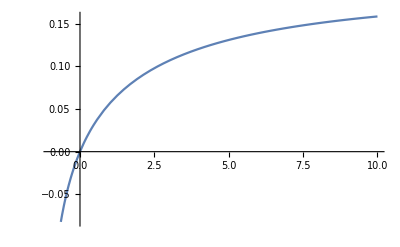

```mathematica
Plot[pfinal[A[lp[k]], B[lm,lp[k],Np]], {k,-0.99,10}]
```

```mathematica
{{d11,o1},{o1,d12}}
```

{{-a^2/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))-(a^2 b^2 (4 a^2-12 a b+11 b^2))/(32 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^2 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))+(√a √(2 π))/(√((2 a^2-5 a b+b^2)/(a-2 b)) √((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2)) √((a π-2 b π)/(2 a^2-6 a b))),-(a^2 (2 a-3 b) b)/(4 √2 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))-(3 a^2 b^3 (8 a^3-36 a^2 b+62 a b^2-39 b^3))/(128 √2 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^3 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))+(a^(3/2) (2 a-3 b) b)/(((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2))^(3/2) ((2 a^2-5 a b+b^2)/(a π-2 b π))^(3/2) (a π-2 b π) √((a π-2 b π)/(2 a^2-6 a b)))},{-(a^2 (2 a-3 b) b)/(4 √2 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))-(3 a^2 b^3 (8 a^3-36 a^2 b+62 a b^2-39 b^3))/(128 √2 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^3 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))+(a^(3/2) (2 a-3 b) b)/(((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2))^(3/2) ((2 a^2-5 a b+b^2)/(a π-2 b π))^(3/2) (a π-2 b π) √((a π-2 b π)/(2 a^2-6 a b))),-(a^2 b^2 (4 a^2-12 a b+11 b^2))/(32 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^2 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))-(3 a^2 b^4 (48 a^4-288 a^3 b+744 a^2 b^2-936 a b^3+467 b^4))/(1024 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^4 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))+(√a b^2 (4 a^2-12 a b+17 b^2) √(π/2))/(√((2 a^2-5 a b+b^2)/(a-2 b)) (4 a^2-12 a b+5 b^2)^2 √((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2)) √((a π-2 b π)/(2 a^2-6 a b)))}}

```mathematica
{{d21,o21,o22},{o21,d22,o23},{o22,o23,d23}}
```

{{(-(2 √(a^2 (a-3 b)))/(2 a-3 b)-(√(a^2 (a-3 b)) b^2)/(2 a-3 b)^3+a^(5/2)/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2))))/(√a),1/(4 √2 √a (2 a-3 b)^4)b (-8 √(a^2 (a-3 b)) (2 a-3 b)^2-12 √(a^2 (a-3 b)) b^2+(a^(5/2) (2 a-3 b)^5)/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))),1/(32 √a (2 a-3 b)^5)3 b^2 (-32 √(a^2 (a-3 b)) (2 a-3 b)^2-80 √(a^2 (a-3 b)) b^2+(a^(5/2) (2 a-3 b)^7)/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^2 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2))))},{1/(4 √2 √a (2 a-3 b)^4)b (-8 √(a^2 (a-3 b)) (2 a-3 b)^2-12 √(a^2 (a-3 b)) b^2+(a^(5/2) (2 a-3 b)^5)/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))),(b^2 (-(32 √(a^2 (a-3 b)))/(2 a-3 b)^3-(144 √(a^2 (a-3 b)) b^2)/(2 a-3 b)^5+(a^(5/2) (4 a^2-12 a b+11 b^2))/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^2 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))))/(32 √a),(3 b^3 (-(128 √(a^2 (a-3 b)))/(2 a-3 b)^4-(960 √(a^2 (a-3 b)) b^2)/(2 a-3 b)^6+(a^(5/2) (8 a^3-36 a^2 b+62 a b^2-39 b^3))/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^3 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))))/(128 √2 √a)},{1/(32 √a (2 a-3 b)^5)3 b^2 (-32 √(a^2 (a-3 b)) (2 a-3 b)^2-80 √(a^2 (a-3 b)) b^2+(a^(5/2) (2 a-3 b)^7)/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^2 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))),(3 b^3 (-(128 √(a^2 (a-3 b)))/(2 a-3 b)^4-(960 √(a^2 (a-3 b)) b^2)/(2 a-3 b)^6+(a^(5/2) (8 a^3-36 a^2 b+62 a b^2-39 b^3))/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^3 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))))/(128 √2 √a),(3 b^4 (-(1536 √(a^2 (a-3 b)))/(2 a-3 b)^5-(19200 √(a^2 (a-3 b)) b^2)/(2 a-3 b)^7+(a^(5/2) (48 a^4-288 a^3 b+744 a^2 b^2-936 a b^3+467 b^4))/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^4 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))))/(1024 √a)}}

```mathematica
{{intd31,into31,into32,into33},{into31,intd32,into34,into35},{into32,into34,intd33,into36},{into33,into35,into36,intd34}}
```

{{(2 √(a^2 (a-3 b)))/(√a (2 a-3 b)),(√2 √(a^2 (a-3 b)) b)/(√a (2 a-3 b)^2),(3 √(a^2 (a-3 b)) b^2)/(√a (2 a-3 b)^3),(15 √(a^2 (a-3 b)) b^3)/(√2 √a (2 a-3 b)^4)},{(√2 √(a^2 (a-3 b)) b)/(√a (2 a-3 b)^2),(√(a^2 (a-3 b)) b^2)/(√a (2 a-3 b)^3),(3 √(a^2 (a-3 b)) b^3)/(√2 √a (2 a-3 b)^4),(15 √(a^2 (a-3 b)) b^4)/(2 √a (2 a-3 b)^5)},{(3 √(a^2 (a-3 b)) b^2)/(√a (2 a-3 b)^3),(3 √(a^2 (a-3 b)) b^3)/(√2 √a (2 a-3 b)^4),(9 √(a^2 (a-3 b)) b^4)/(2 √a (2 a-3 b)^5),(45 √(a^2 (a-3 b)) b^5)/(2 √2 √a (2 a-3 b)^6)},{(15 √(a^2 (a-3 b)) b^3)/(√2 √a (2 a-3 b)^4),(15 √(a^2 (a-3 b)) b^4)/(2 √a (2 a-3 b)^5),(45 √(a^2 (a-3 b)) b^5)/(2 √2 √a (2 a-3 b)^6),(225 √(a^2 (a-3 b)) b^6)/(4 √a (2 a-3 b)^7)}}

```mathematica
1-d11-d12-d21-d22-d23-intd31-intd32-intd33-intd34
```

1-(2 √(a^2 (a-3 b)))/(√a (2 a-3 b))-(√(a^2 (a-3 b)) b^2)/(√a (2 a-3 b)^3)-(9 √(a^2 (a-3 b)) b^4)/(2 √a (2 a-3 b)^5)-(225 √(a^2 (a-3 b)) b^6)/(4 √a (2 a-3 b)^7)+a^2/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))+(a^2 b^2 (4 a^2-12 a b+11 b^2))/(16 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^2 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))+(3 a^2 b^4 (48 a^4-288 a^3 b+744 a^2 b^2-936 a b^3+467 b^4))/(1024 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^4 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))-(-(2 √(a^2 (a-3 b)))/(2 a-3 b)-(√(a^2 (a-3 b)) b^2)/(2 a-3 b)^3+a^(5/2)/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2))))/(√a)-(b^2 (-(32 √(a^2 (a-3 b)))/(2 a-3 b)^3-(144 √(a^2 (a-3 b)) b^2)/(2 a-3 b)^5+(a^(5/2) (4 a^2-12 a b+11 b^2))/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^2 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))))/(32 √a)-(3 b^4 (-(1536 √(a^2 (a-3 b)))/(2 a-3 b)^5-(19200 √(a^2 (a-3 b)) b^2)/(2 a-3 b)^7+(a^(5/2) (48 a^4-288 a^3 b+744 a^2 b^2-936 a b^3+467 b^4))/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^4 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))))/(1024 √a)-(√a b^2 (4 a^2-12 a b+17 b^2) √(π/2))/(√((2 a^2-5 a b+b^2)/(a-2 b)) (4 a^2-12 a b+5 b^2)^2 √((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2)) √((a π-2 b π)/(2 a^2-6 a b)))-(√a √(2 π))/(√((2 a^2-5 a b+b^2)/(a-2 b)) √((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2)) √((a π-2 b π)/(2 a^2-6 a b)))

### Create Density Operator for MMRDO

```mathematica
matrixvac[a_,b_]:= 1-(2 √(a^2 (a-3 b)))/(√a (2 a-3 b))-(√(a^2 (a-3 b)) b^2)/(√a (2 a-3 b)^3)-(9 √(a^2 (a-3 b)) b^4)/(2 √a (2 a-3 b)^5)-(225 √(a^2 (a-3 b)) b^6)/(4 √a (2 a-3 b)^7)+a^2/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))+(a^2 b^2 (4 a^2-12 a b+11 b^2))/(16 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^2 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))+(3 a^2 b^4 (48 a^4-288 a^3 b+744 a^2 b^2-936 a b^3+467 b^4))/(1024 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^4 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))-(-(2 √(a^2 (a-3 b)))/(2 a-3 b)-(√(a^2 (a-3 b)) b^2)/(2 a-3 b)^3+a^(5/2)/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2))))/(√a)-1/(32 √a)b^2 (-(32 √(a^2 (a-3 b)))/(2 a-3 b)^3-(144 √(a^2 (a-3 b)) b^2)/(2 a-3 b)^5+(a^(5/2) (4 a^2-12 a b+11 b^2))/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^2 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2))))-1/(1024 √a)3 b^4 (-(1536 √(a^2 (a-3 b)))/(2 a-3 b)^5-(19200 √(a^2 (a-3 b)) b^2)/(2 a-3 b)^7+(a^(5/2) (48 a^4-288 a^3 b+744 a^2 b^2-936 a b^3+467 b^4))/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^4 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2))))-(√a b^2 (4 a^2-12 a b+17 b^2) √(π/2))/(√((2 a^2-5 a b+b^2)/(a-2 b)) (4 a^2-12 a b+5 b^2)^2 √((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2)) √((a π-2 b π)/(2 a^2-6 a b)))-(√a √(2 π))/(√((2 a^2-5 a b+b^2)/(a-2 b)) √((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2)) √((a π-2 b π)/(2 a^2-6 a b)))
```

```mathematica
matrixone[a_,b_]:={{-a^2/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))-(a^2 b^2 (4 a^2-12 a b+11 b^2))/(32 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^2 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))+(√a √(2 π))/(√((2 a^2-5 a b+b^2)/(a-2 b)) √((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2)) √((a π-2 b π)/(2 a^2-6 a b))),-(a^2 (2 a-3 b) b)/(4 √2 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))-(3 a^2 b^3 (8 a^3-36 a^2 b+62 a b^2-39 b^3))/(128 √2 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^3 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))+(a^(3/2) (2 a-3 b) b)/(((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2))^(3/2) ((2 a^2-5 a b+b^2)/(a π-2 b π))^(3/2) (a π-2 b π) √((a π-2 b π)/(2 a^2-6 a b)))},{-(a^2 (2 a-3 b) b)/(4 √2 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))-(3 a^2 b^3 (8 a^3-36 a^2 b+62 a b^2-39 b^3))/(128 √2 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^3 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))+(a^(3/2) (2 a-3 b) b)/(((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2))^(3/2) ((2 a^2-5 a b+b^2)/(a π-2 b π))^(3/2) (a π-2 b π) √((a π-2 b π)/(2 a^2-6 a b))),-(a^2 b^2 (4 a^2-12 a b+11 b^2))/(32 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^2 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))-(3 a^2 b^4 (48 a^4-288 a^3 b+744 a^2 b^2-936 a b^3+467 b^4))/(1024 √((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^4 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))+(√a b^2 (4 a^2-12 a b+17 b^2) √(π/2))/(√((2 a^2-5 a b+b^2)/(a-2 b)) (4 a^2-12 a b+5 b^2)^2 √((a (4 a^2-12 a b+5 b^2))/(2 a^2-5 a b+b^2)) √((a π-2 b π)/(2 a^2-6 a b)))}}
```

```mathematica
matrixtwo[a_,b_]:={{(-(2 √(a^2 (a-3 b)))/(2 a-3 b)-(√(a^2 (a-3 b)) b^2)/(2 a-3 b)^3+a^(5/2)/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2))))/(√a),1/(4 √2 √a (2 a-3 b)^4)b (-8 √(a^2 (a-3 b)) (2 a-3 b)^2-12 √(a^2 (a-3 b)) b^2+(a^(5/2) (2 a-3 b)^5)/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))),1/(32 √a (2 a-3 b)^5)3 b^2 (-32 √(a^2 (a-3 b)) (2 a-3 b)^2-80 √(a^2 (a-3 b)) b^2+(a^(5/2) (2 a-3 b)^7)/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^2 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2))))},{1/(4 √2 √a (2 a-3 b)^4)b (-8 √(a^2 (a-3 b)) (2 a-3 b)^2-12 √(a^2 (a-3 b)) b^2+(a^(5/2) (2 a-3 b)^5)/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))),1/(32 √a)b^2 (-(32 √(a^2 (a-3 b)))/(2 a-3 b)^3-(144 √(a^2 (a-3 b)) b^2)/(2 a-3 b)^5+(a^(5/2) (4 a^2-12 a b+11 b^2))/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^2 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))),1/(128 √2 √a)3 b^3 (-(128 √(a^2 (a-3 b)))/(2 a-3 b)^4-(960 √(a^2 (a-3 b)) b^2)/(2 a-3 b)^6+(a^(5/2) (8 a^3-36 a^2 b+62 a b^2-39 b^3))/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^3 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2))))},{1/(32 √a (2 a-3 b)^5)3 b^2 (-32 √(a^2 (a-3 b)) (2 a-3 b)^2-80 √(a^2 (a-3 b)) b^2+(a^(5/2) (2 a-3 b)^7)/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^2 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))),1/(128 √2 √a)3 b^3 (-(128 √(a^2 (a-3 b)))/(2 a-3 b)^4-(960 √(a^2 (a-3 b)) b^2)/(2 a-3 b)^6+(a^(5/2) (8 a^3-36 a^2 b+62 a b^2-39 b^3))/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^3 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))),1/(1024 √a)3 b^4 (-(1536 √(a^2 (a-3 b)))/(2 a-3 b)^5-(19200 √(a^2 (a-3 b)) b^2)/(2 a-3 b)^7+(a^(5/2) (48 a^4-288 a^3 b+744 a^2 b^2-936 a b^3+467 b^4))/(√((a-b)/(a-3 b)) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^4 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2))))}}
```

```mathematica
matrixthree[a_,b_]:={{(2 √(a^2 (a-3 b)))/(√a (2 a-3 b)),(√2 √(a^2 (a-3 b)) b)/(√a (2 a-3 b)^2),(3 √(a^2 (a-3 b)) b^2)/(√a (2 a-3 b)^3),(15 √(a^2 (a-3 b)) b^3)/(√2 √a (2 a-3 b)^4)},{(√2 √(a^2 (a-3 b)) b)/(√a (2 a-3 b)^2),(√(a^2 (a-3 b)) b^2)/(√a (2 a-3 b)^3),(3 √(a^2 (a-3 b)) b^3)/(√2 √a (2 a-3 b)^4),(15 √(a^2 (a-3 b)) b^4)/(2 √a (2 a-3 b)^5)},{(3 √(a^2 (a-3 b)) b^2)/(√a (2 a-3 b)^3),(3 √(a^2 (a-3 b)) b^3)/(√2 √a (2 a-3 b)^4),(9 √(a^2 (a-3 b)) b^4)/(2 √a (2 a-3 b)^5),(45 √(a^2 (a-3 b)) b^5)/(2 √2 √a (2 a-3 b)^6)},{(15 √(a^2 (a-3 b)) b^3)/(√2 √a (2 a-3 b)^4),(15 √(a^2 (a-3 b)) b^4)/(2 √a (2 a-3 b)^5),(45 √(a^2 (a-3 b)) b^5)/(2 √2 √a (2 a-3 b)^6),(225 √(a^2 (a-3 b)) b^6)/(4 √a (2 a-3 b)^7)}}
```

```mathematica
matrixdim={{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}
```

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

```mathematica
Eigenvalues[matrixtwo[A[lp[-0.99]], B[lm,lp[-0.99],Np]]]
```

{0.00499669,0.0000376326,5.55598×10^-8}

```mathematica
fullmatrix[k_]:=Fold[ArrayFlatten[{{#,0},{0,#2}}]&,matrixvac[A[lp[k]], B[lm,lp[k],Np]],{matrixone[A[lp[k]], B[lm,lp[k],Np]],matrixtwo[A[lp[k]], B[lm,lp[k],Np]],matrixthree[A[lp[k]], B[lm,lp[k],Np]], matrixdim}]
```

```mathematica
Eigenvalues[fullmatrix[50.3]]
```

{0.687122,0.230409,0.0770228,0.00333966,0.0020838,0.000022228,2.75422×10^-8,-1.71518×10^-17,1.5546×10^-17,-7.06782×10^-18,0.,0.,0.,0.,0.,0.}

```mathematica
fullmatrix[100.6] //MatrixForm
```

(0.291322 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.0586508 | 0.0429372 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.0429372 | 0.0366018 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.00127621 | 0.00126544 | 0.00175728 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.00126544 | 0.00126843 | 0.00178087 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.00175728 | 0.00178087 | 0.00252835 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.573094 | 0.110696 | 0.0641448 | 0.0619496 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.110696 | 0.0213816 | 0.0123899 | 0.0119659 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.0641448 | 0.0123899 | 0.00717955 | 0.00693384 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.0619496 | 0.0119659 | 0.00693384 | 0.00669655 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
matexportfunct[i_, ind_]:=Export["/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/"<>"data_m02_k"<>ToString[ind]<>".mat", fullmatrix[i]]
```

```mathematica
kappalogrange[i_]:= If[i≤1, i, 10^(i-1)]
kappamin = -0.99;
kappamax = 6;
kappagran = 0.1;
kappalist = Table[kappalogrange[k], {k,kappamin, kappamax, kappagran}];
```

```mathematica
Table[matexportfunct[kappalist[[i]],i],{i,1,Length[kappalist]}]
```

{/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k1.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k2.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k3.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k4.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k5.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k6.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k7.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k8.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k9.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k10.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k11.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k12.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k13.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k14.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k15.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k16.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k17.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k18.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k19.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k20.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k21.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k22.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k23.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k24.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k25.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k26.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k27.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k28.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k29.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k30.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k31.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k32.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k33.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k34.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k35.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k36.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k37.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k38.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k39.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k40.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k41.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k42.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k43.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k44.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k45.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k46.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k47.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k48.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k49.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k50.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k51.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k52.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k53.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k54.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k55.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k56.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k57.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k58.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k59.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k60.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k61.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k62.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k63.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k64.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k65.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k66.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k67.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k68.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k69.mat,/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results Bosons N3d1/mode-mode-entanglement/matlab_data_n3d1_m02/data_m02_k70.mat}